# Maternal Effects and Maternal Age

Bram Kuijper & Rufus A. Johnstone

## Parameters and initialization

Clear memory:

```mathematica
Clear["Global`*"]
```

- Patch frequncies f_(x,i,j,k)
x: environment e_1 or e_2 (here annotated as a, b)
i: number of young breeders adapted to local environment
j: number of young breeders maladapted to local environment
k: number of old breeders adapted to local environment

```mathematica
f[e_,a1_,m1_,a2_,m2_]:=fx[e,a1,m1,a2]
```

- Switching rates
s_1=s_(e_1→e_2)
s_2=s_(e_2→e_1)

```mathematica
st={s1,s2};
s[es_]:=st[[es]]
```

Specification of the evolutionary variables

- Dispersal locus
mx: resident dispersal rates
dmx: δ, slight difference between mutant and resident dispersal rates

```mathematica
mx={{{mt,mt},{mt,mt}},{{mt,mt},{mt,mt}}};
dmx={{{dmt,dmt},{dmt,dmt}},{{dmt,dmt},{dmt,dmt}}};
m[es_,state_,age_]:=mx[[age+1,es,1+state]];
dm[es_,state_,age_]:=dmx[[age+1,es,1+state]];
varlistM:={mt}; (* definitions needed later for function specification *)
varlistdM:={dmt};
arglistM:=ms__Real;
```

- Phenotype-dependent switching
px: table of probabilities that females with a particular phenotype produce offspring of a different phenotype than their own. 
dpx: same, but now as a function of a slight mutant difference relative to resident
p_1,p_2: probability of producing z_1-offspring  for z_1 and z_2 parents respectively
Q: `trembling hand’ error to avoid local maxima (sensu Selten 1975 Int J Game Theor 4: 25-55)

p[es,ad]: lookup function connecting a female’s environment es and her adapted/maladapted state ad to values of px 
For example, p[1,0] reflects a female living in environment e_1 with ‘adaptedness’=0 (i.e., maladapted). In other words, this is a z_2-female (which is adapted to environment e_2). See main text.

```mathematica
px=
{
{
{(1-Q)p20+Q(1-p20),(1-Q)(1-p10)+Q p10},
{(1-Q)(1-p10)+Q p10,(1-Q)p20+Q(1-p20)}
},
{
{(1-Q)p21+Q(1-p21),(1-Q)(1-p11)+Q p11},
{(1-Q)(1-p11)+Q p11,(1-Q)p21+Q(1-p21)}
}
};
dpx=
{
{
{(1-Q)p20-Q dp20,-(1-Q)dp10+Q dp10},
{-(1-Q)dp10+Q dp10,(1-Q)dp20+-dp20 Q}
},
{
{(1-Q)dp21+-dp21 Q,-dp11(1-Q)+Q dp11},
{-(1-Q)dp11+Q dp11,(1-Q)dp21+-dp21 Q}
}
};
p[es_,ad_,age_]:=px[[age+1,es,1+ad]];
dp[es_,ad_,age_]:=dpx[[age+1,es,1+ad]]
```

- Mortality selection parameters
c_1,c_2: mortality parameters for maladapted individuals (mortality for adapted individuals = 1)
For examp

```mathematica
dx={{{1/(1-c1),1},{1/(1-c2),1}},{{1/(1-c3),1},{1/(1-c4),1}}};
d[es_,state_,age_]:=dx[[age+1,es,1+state]]
```

- Fecundity selection,
(will be considered in a follow-up paper, Kuijper & Johnstone, in preparation). In the current paper q_1=q_2=0 (i.e., no fecundity selection)

```mathematica
gx={{{1,1/(1-q1)},{1,1/(1-q2)}},{{1,1/(1-q1)},{1,1/(1-q2)}}} ;
g[es_,state_,age_]:=gx[[age+1,es,1+state]]
```

- Number of breeders per patch

```mathematica
n=2
```

2

## Patch frequencies

```mathematica
localad[es_,a1_,m1_,a2_]:=a1/n g[es,1,0](1-p[es,1,0])(1-m[es,1,0])+a2/n g[es,1,1](1-p[es,1,1])(1-m[es,1,1])+m1/n g[es,0,0]p[es,0,0](1-m[es,0,0])+(n-a2-a1-m1)/n g[es,0,1]p[es,0,1](1-m[es,0,1])
localmad[es_,a1_,m1_,a2_]:=a1/n g[es,1,0]p[es,1,0](1-m[es,1,0])+a2/n g[es,1,1]p[es,1,1](1-m[es,1,1])+m1/n g[es,0,0](1-p[es,0,0])(1-m[es,0,0])+(n-a2-a1-m1)/n g[es,0,1](1-p[es,0,1])(1-m[es,0,1])
```

- Migrant juveniles arriving in an environment to which they are adapted (dispad) or maladapted (dispmad)
k: cost of dispersal. Calculations below are  derived in the same fashion as calculations involving philopatric juveniles. See also in-line comments

```mathematica
dispad[es_]:=(* probability that a migrant migrates into environment es where it is adapted *)
Simplify[(1-k)*Sum[(* sum over environments *)
Sum[(* sum over number of adapted breeders *)
If[es==esSum,
f[esSum,a1,m1,a2,n-a1-m1-a2](a1/n g[esSum,1,0](1-p[esSum,1,0])m[esSum,1,0]+m1/n g[esSum,0,0]p[esSum,0,0]m[esSum,0,0]+a2/n g[esSum,1,1](1-p[esSum,1,1])m[esSum,1,1]+(n-a2-a1-m1)/n g[esSum,0,1]p[esSum,0,1]m[esSum,0,1]),(* environment same as target *)
f[esSum,a1,m1,a2,n-a1-m1-a2](a1/n g[esSum,1,0]p[esSum,1,0]m[esSum,1,0]+m1/n g[esSum,0,0](1-p[esSum,0,0])m[esSum,0,0]+a2/n g[esSum,1,1]p[esSum,1,1]m[esSum,1,1]+(n-a2-a1-m1)/n g[esSum,0,1](1-p[esSum,0,1])m[esSum,0,1]) (* environment different from target *)
],
{a1,0,n},{m1,0,n-a1},{a2,0,n-a1-m1}],
{esSum,1,2}]];
dispmad[es_]:=(* probability that a migrant migrates into environment es where it is maladapted *)
Simplify[(1-k)*Sum[(* sum over environments *)
Sum[(* sum over number of adapted breeders *)
If[es==esSum,
f[esSum,a1,m1,a2,n-a1-m1-a2](a1/n g[esSum,1,0]p[esSum,1,0]m[esSum,1,0]+m1/n g[esSum,0,0](1-p[esSum,0,0])m[esSum,0,0]+a2/n g[esSum,1,1]p[esSum,1,1]m[esSum,1,1]+(n-a2-a1-m1)/n g[esSum,0,1](1-p[esSum,0,1])m[esSum,0,1]) ,
(* environment same as target *)
f[esSum,a1,m1,a2,n-a1-m1-a2](a1/n g[esSum,1,0](1-p[esSum,1,0])m[esSum,1,0]+m1/n g[esSum,0,0]p[esSum,0,0]m[esSum,0,0]+a2/n g[esSum,1,1](1-p[esSum,1,1])m[esSum,1,1]+(n-a2-a1-m1)/n g[esSum,0,1]p[esSum,0,1]m[esSum,0,1])
(* environment different from target *)
],
{a1,0,n},{m1,0,n-a1},{a2,0,n-a1-m1}],
{esSum,1,2}]];
```

- Total number of locally competing juveniles:

```mathematica
localcomptotal[es_,a1_,m1_,a2_]:=localad[es,a1,m1,a2]+localmad[es,a1,m1,a2]+dispad[es]+dispmad[es]
```

ap[es,a]: Probability that any adapted juvenile will win competition over breeding spots in an environment of type es with a adapted adult breeders.

```mathematica
ap[es_,a1_,m1_,a2_,m2_]:=(localad[es,a1,m1,a2]+dispad[es])/localcomptotal[es,a1,m1,a2]
```

- Differential equations for the patch frequencies
Each event (switching, mortality of different types of breeders) is highlighted by an in-line comment. Table contains right hand side of differential equations:

```mathematica
tablerecPlain=Table[
With[{m2=n-a1-a2-m1},s[3-es] f[3-es,m1,a1,m2,a2]-s[es] f[es,a1,m1,a2,m2] (* change due to environmental switching *)
+If[a1-1≥0&&m1+1≤n,(m1+1)d[es,0,0]ap[es,a1-1,m1+1,a2,m2]f[es,a1-1,m1+1,a2,m2],0]
(* maladapted juvenile breeder dies, replaced by adapted juvenile breeder on a m1+1,a1-1 patch *)
-m1 d[es,0,0]ap[es,a1,m1,a2,m2]f[es,a1,m1,a2,m2]
(* maladapted juvenile breeder dies, replaced by an adapted juvenile breeder on a m1,a1 patch *)
+If[m1+1≤n&&m2-1≥0,(m1+1)f[es,a1,m1+1,a2,m2-1],0]
(* maladapted juvenile breeder survives to become a maladapted adult breeder on a m1+1,m2-1 patch *)
-m1 f[es,a1,m1,a2,m2]
(* maladapted juvenile breeder survives to become a maladapted adult breeder on a m1,m2 patch *)
+If[a1+1≤n&&m1-1≥0,(a1+1)d[es,1,0](1-ap[es,a1+1,m1-1,a2,m2])f[es,a1+1,m1-1,a2,m2],0]
(* adapted juvenile breeder dies and is replaced by a maladapted breeder on a a1+1,m1-1 patch *)
-a1 d[es,1,0](1-ap[es,a1,m1,a2,m2])f[es,a1,m1,a2,m2]
(* adapted juvenile breeder dies and is replaced by a maladapted breeder on a a1,m1 patch *)
+If[a1+1≤n&&a2-1≥0,(a1+1)f[es,a1+1,m1,a2-1,m2],0]
(* adapted juvenile breeder survives and becomes an adapted adult breeder on a a1+1,a2-1 patch *)
-a1 f[es,a1,m1,a2,m2]
(* adapted juvenile breeder survives and becomes an adapted adult breeder on a a1,a2 patch *)
+If[m2+1≤n&&a1-1≥0,(m2+1)d[es,0,1]ap[es,a1-1,m1,a2,m2+1]f[es,a1-1,m1,a2,m2+1],0]
(* maladapted adult breeder dies and is replaced by an adapted juvenile breeder on a a1-1,m2+1 patch *)
+If[m2+1≤n&&m1-1≥0,(m2+1)d[es,0,1](1-ap[es,a1,m1-1,a2,m2+1])f[es,a1,m1-1,a2,m2+1],0]
(* maladapted adult breeder dies and is replaced by a maladapted juvenile breeder on a m1-1,m2+1 patch *)
-m2 d[es,0,1]f[es,a1,m1,a2,m2]
(* maladapted adult breeder dies and is replaced by a juvenile breeder on a a1,m1,m2 patch *)
+If[a2+1≤n&&a1-1≥0,(a2+1)d[es,1,1]ap[es,a1-1,m1,a2+1,m2]f[es,a1-1,m1,a2+1,m2],0]
(* adapted adult breeder dies and is replaced by an adapted juvenile breeder on a a1-1,a2+1 patch *)
+If[a2+1≤n&&m1-1≥0,(a2+1)d[es,1,1](1-ap[es,a1,m1-1,a2+1,m2])f[es,a1,m1-1,a2+1,m2],0]
(* adapted adult breeder dies and is replaced by a maladapted juvenile breeder on a m1-1,a2+1 patch *)
-a2 d[es,1,1]f[es,a1,m1,a2,m2]
(* adapted adult breeder dies and is replaced by a juvenile breeder on a a1,m1,a2 patch *)
],{es,1,2},{a1,0,n},{m1,0,n-a1},{a2,0,n-a1-m1}];
```

Table specification for numerical solving:

```mathematica
Dimensions[tablerec]
```

{}

```mathematica
tablerec=Flatten[Table[H==0,{H,Flatten[tablerecPlain]}]];
```

```mathematica
tablerec[[1]]
```

-(2 fx[1,0,0,0])/(1-c3)-s1 fx[1,0,0,0]+fx[1,0,1,0]+s2 fx[2,0,0,2]==0

```mathematica
ftab=Table[With[{m2=n-a1-m1-a2},f[es,a1,m1,a2,m2]],{es,1,2},{a1,0,n},{m1,0,n-a1},{a2,0,n-a1-m1}]//Flatten
```

{fx[1,0,0,0],fx[1,0,0,1],fx[1,0,0,2],fx[1,0,1,0],fx[1,0,1,1],fx[1,0,2,0],fx[1,1,0,0],fx[1,1,0,1],fx[1,1,1,0],fx[1,2,0,0],fx[2,0,0,0],fx[2,0,0,1],fx[2,0,0,2],fx[2,0,1,0],fx[2,0,1,1],fx[2,0,2,0],fx[2,1,0,0],fx[2,1,0,1],fx[2,1,1,0],fx[2,2,0,0]}

```mathematica
feqtab=ReplacePart[Flatten[tablerec],Total[ftab]==1,1];
feqtabalt=ReplacePart[Flatten[tablerec],Total[ftab]==1,5];
```

```mathematica
feqtabPlain=ReplacePart[Flatten[tablerecPlain],Total[ftab]-1,1];
```

```mathematica
frootstartvals=Table[{xi,1/Length[ftab]},{xi,ftab}]
```

{{fx[1,0,0,0],1/20},{fx[1,0,0,1],1/20},{fx[1,0,0,2],1/20},{fx[1,0,1,0],1/20},{fx[1,0,1,1],1/20},{fx[1,0,2,0],1/20},{fx[1,1,0,0],1/20},{fx[1,1,0,1],1/20},{fx[1,1,1,0],1/20},{fx[1,2,0,0],1/20},{fx[2,0,0,0],1/20},{fx[2,0,0,1],1/20},{fx[2,0,0,2],1/20},{fx[2,0,1,0],1/20},{fx[2,0,1,1],1/20},{fx[2,0,2,0],1/20},{fx[2,1,0,0],1/20},{fx[2,1,0,1],1/20},{fx[2,1,1,0],1/20},{fx[2,2,0,0],1/20}}

- Numerically solve for the equilibrium patch frequencies

```mathematica
ans1test[{s1s_,s2s_},{c1s_,c2s_,c3s_,c4s_},{q1s_,q2s_},{m_},{p10s_,p11s_,p20s_,p21s_},ks_,Qs_]:=
feqtab/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,c3->c3s,c4->c4s,Q->Qs,p10->p10s,p11->p11s,p20->p20s,p21->p21s,mt->m}]
```

```mathematica
ans1[{s1s_,s2s_},{c1s_,c2s_,c3s_,c4s_},{q1s_,q2s_},{m_},{p10s_,p11s_,p20s_,p21s_},ks_,Qs_]:=
FindRoot[feqtab/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,c3->c3s,c4->c4s,Q->Qs,p10->p10s,p11->p11s,p20->p20s,p21->p21s,mt->m}],frootstartvals]
```

```mathematica
ans1alt[{s1s_,s2s_},{c1s_,c2s_,c3s_,c4s_},{q1s_,q2s_},{m_},{p10s_,p11s_,p20s_,p21s_},ks_,Qs_]:=
FindRoot[feqtabalt/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,c3->c3s,c4->c4s,Q->Qs,p10->p10s,p11->p11s,p20->p20s,p21->p21s,mt->m}],frootstartvals]
```

```mathematica
ans1[{0.5,0.5},{0.5,0.5,0.5,0.5},{0,0},{.3},{0.3,0.5,0.3,0.5},0.1,0.005]
```

{fx[1,0,0,0]→0.0194707,fx[1,0,0,1]→0.0386538,fx[1,0,0,2]→0.0263002,fx[1,0,1,0]→0.0615933,fx[1,0,1,1]→0.064591,fx[1,0,2,0]→0.055045,fx[1,1,0,0]→0.0533607,fx[1,1,0,1]→0.061689,fx[1,1,1,0]→0.0854658,fx[1,2,0,0]→0.0338304,fx[2,0,0,0]→0.00812311,fx[2,0,0,1]→0.0346735,fx[2,0,0,2]→0.0520499,fx[2,0,1,0]→0.0234039,fx[2,0,1,1]→0.0601038,fx[2,0,2,0]→0.0156128,fx[2,1,0,0]→0.0419266,fx[2,1,0,1]→0.120389,fx[2,1,1,0]→0.0671251,fx[2,2,0,0]→0.076592}

```mathematica
ans1alt[{0.5,0.5},{0.5,0.5,0.5,0.5},{0,0},{.3},{0.3,0.5,0.3,0.5},0.1,0.005]
```

{fx[1,0,0,0]→0.0194707,fx[1,0,0,1]→0.0386538,fx[1,0,0,2]→0.0263002,fx[1,0,1,0]→0.0615933,fx[1,0,1,1]→0.064591,fx[1,0,2,0]→0.055045,fx[1,1,0,0]→0.0533607,fx[1,1,0,1]→0.061689,fx[1,1,1,0]→0.0854658,fx[1,2,0,0]→0.0338304,fx[2,0,0,0]→0.00812311,fx[2,0,0,1]→0.0346735,fx[2,0,0,2]→0.0520499,fx[2,0,1,0]→0.0234039,fx[2,0,1,1]→0.0601038,fx[2,0,2,0]→0.0156128,fx[2,1,0,0]→0.0419266,fx[2,1,0,1]→0.120389,fx[2,1,1,0]→0.0671251,fx[2,2,0,0]→0.076592}

## Reproductive values

- Table of the reproductive values: v_ijk:
reproductive value in environment i, with focal individual being either locally maladapted  j=0 or adapted (j=1) in the presence of k adapted (and n-k maladapted individuals)

- Adapted/Maladapted individuals produced by nonfocal individual on the patch

```mathematica
localadother[es_,a1other_,m1other_,a2other_]:=a1other/n g[es,1,0](1-p[es,1,0])(1-m[es,1,0])+m1other/n g[es,0,0]p[es,0,0](1-m[es,0,0])+a2other/n g[es,1,1](1-p[es,1,1])(1-m[es,1,1])+(n-1-a1other-m1other-a2other)/n g[es,0,1]p[es,0,1](1-m[es,0,1])
localmadother[es_,a1other_,m1other_,a2other_]:=a1other/n g[es,1,0]p[es,1,0](1-m[es,1,0])+m1other/n g[es,0,0](1-p[es,0,0])(1-m[es,0,0])+a2other/n g[es,1,1]p[es,1,1](1-m[es,1,1])+(n-1-a1other-m1other-a2other)/n g[es,0,1](1-p[es,0,1])(1-m[es,0,1])
```

- Table with differential equations of the reproductive values
See in-line comments

### Reproductive values: juveniles

```mathematica
veqtabPlainJuv=Table[
With[{m2other=n-1-a1other-m1other-a2other},
s[es](v[3-es,0,1-aself,m1other,a1other,m2other]-v[es,0,aself,a1other,m1other,a2other])
(* envt change *)
+d[es,aself,0]((1-m[es,aself,0])(1/n)p[es,aself,0]g[es,aself,0])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other](v[es,0,1-aself,a1other,m1other,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 1a. focal juvenile breeder dies, replaced by own offspring of a different type *)
+d[es,aself,0](1-((1-m[es,aself,0])(1/n)g[es,aself,0])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other])(-v[es,0,aself,a1other,m1other,a2other])
(* 1b. focal juvenile breeder dies, replaced by other offspring *)
+(v[es,1,aself,a1other,m1other,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 1c. focal juvenile adapted breeder matures to the next stage *)
+a1other d[es,1,0]((1-m[es,aself,0])(1/n)(1-p[es,aself,0])g[es,aself,0])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other](2v[es,0,aself,a1other-1+aself,m1other+1-aself,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 2a. adapted nonfocal juvenile breeder dies, replaced by focal's offspring of the same type as focal *)
+a1other d[es,1,0]((1-m[es,aself,0])(1/n)p[es,aself,0]g[es,aself,0])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other](v[es,0,1-aself,a1other-1+aself,m1other+1-aself,a2other]+v[es,0,aself,a1other-1+1-aself,m1other+aself,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 2b. adapted nonfocal juvenile breeder dies, replaced by focal's offspring of a different type as focal *)
+a1other d[es,1,0]((localmadother[es,a1other,m1other,a2other]+dispmad[es])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other])(v[es,0,aself,a1other-1,m1other+1,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 2c. adapted nonfocal juvenile breeder dies, replaced by nonfocal offspring that is maladapted *)
+a1other (v[es,0,aself,a1other-1,m1other,a2other+1]-v[es,0,aself,a1other,m1other,a2other])
(* 2d. adapted nonfocal juvenile matures to adult breedership *)
+m1other d[es,0,0]((1-m[es,aself,0])(1/n)(1-p[es,aself,0])g[es,aself,0])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other](2v[es,0,aself,a1other+aself,m1other-1+1-aself,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 3a. maladapted nonfocal juvenile breeder dies, replaced by focal's offspring of the same phenotype as focal *)
+m1other d[es,0,0]((1-m[es,aself,0])(1/n)p[es,aself,0]g[es,aself,0])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other](v[es,0,1-aself,a1other+aself,m1other-1+1-aself,a2other]+v[es,0,aself,a1other+1-aself,m1other-1+aself,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 3b. maladapted nonfocal juvenile breeder dies, replaced by focal's offspring of a different phenotype as focal *)
+m1other d[es,0,0]((localadother[es,a1other,m1other,a2other]+dispad[es])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other])(v[es,0,aself,a1other+1,m1other-1,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 3c. maladapted nonfocal juvenile breeder dies, replaced by nonfocal offspring that is adapted *)
+m1other (v[es,0,aself,a1other,m1other-1,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 3d. maladapted nonfocal juvenile breeder survives to adulthood *)
+a2other d[es,1,1]((1-m[es,aself,0])(1/n)p[es,aself,0]g[es,aself,0])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other](v[es,0,aself,a1other+1-aself,m1other+aself,a2other-1]+v[es,0,1-aself,a1other+aself,m1other+1-aself,a2other-1]-v[es,0,aself,a1other,m1other,a2other])
(* 4a. adapted adult nonfocal breeder dies, replaced by focal offspring of a different type than focal *)
+a2other d[es,1,1]((1-m[es,aself,0])(1/n)(1-p[es,aself,0])g[es,aself,0])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other](2v[es,0,aself,a1other+aself,m1other+1-aself,a2other-1]-v[es,0,aself,a1other,m1other,a2other])
(* 4b. adapted adult nonfocal breeder dies, replaced by focal offspring of the same type as focal *)
+a2other d[es,1,1]((localadother[es,a1other,m1other,a2other]+dispad[es])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other])(v[es,0,aself,a1other+1,m1other,a2other-1]-v[es,0,aself,a1other,m1other,a2other])
(* 4c. adapted adult nonfocal breeder dies, replaced by adapted nonfocal offspring *)
+a2other d[es,1,1]((localmadother[es,a1other,m1other,a2other]+dispmad[es])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other])(v[es,0,aself,a1other,m1other+1,a2other-1]-v[es,0,aself,a1other,m1other,a2other])
(* 4d. adapted adult nonfocal breeder dies, replaced by maladapted nonfocal offspring *)
+m2other d[es,0,1]((1-m[es,aself,0])(1/n)p[es,aself,0]g[es,aself,0])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other](v[es,0,aself,a1other+1-aself,m1other+aself,a2other]+v[es,0,1-aself,a1other+aself,m1other+1-aself,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 5a. maladapted adult nonfocal breeder dies, replaced by focal offspring of a different type than focal *)
+m2other d[es,0,1]((1-m[es,aself,0])(1/n)(1-p[es,aself,0])g[es,aself,0])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other](2v[es,0,aself,a1other+aself,m1other+1-aself,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 5b. maladapted adult nonfocal breeder dies, replaced by focal offspring of the same type as focal *)
+m2other d[es,0,1]((localadother[es,a1other,m1other,a2other]+dispad[es])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other])(v[es,0,aself,a1other+1,m1other,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 5c. maladapted adult nonfocal breeder dies, replaced by adapted focal offspring *)
+m2other d[es,0,1]((localmadother[es,a1other,m1other,a2other]+dispmad[es])/localcomptotal[es,a1other+aself,m1other+1-aself,a2other])(v[es,0,aself,a1other,m1other+1,a2other]-v[es,0,aself,a1other,m1other,a2other])
(* 5d. maladapted adult nonfocal breeder dies, replaced by adapted focal offspring *)
+(1/n)g[es,aself,0](1-k)m[es,aself,0]Sum[With[{zm2=n-za1-zm1-za2},f[zes,za1,zm1,za2,zm2](
za1 d[zes,1,0](
(1-p[es,aself,0])/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,aself,1-aself],za1-1,zm1,za2]+p[es,aself,0]/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,1-aself,aself],za1-1,zm1,za2]
)
+zm1 d[zes,0,0](
(1-p[es,aself,0])/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,aself,1-aself],za1,zm1-1,za2]+p[es,aself,0]/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,1-aself,aself],za1,zm1-1,za2]
)
+za2 d[zes,1,1](
(1-p[es,aself,0])/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,aself,1-aself],za1,zm1,za2-1]+p[es,aself,0]/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,1-aself,aself],za1,zm1,za2-1]
)
+zm2 d[zes,0,1](
(1-p[es,aself,0])/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,aself,1-aself],za1,zm1,za2]+p[es,aself,0]/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,1-aself,aself],za1,zm1,za2]
)
)],{zes,1,2},{za1,0,n},{zm1,0,n-za1},{za2,0,n-za1-zm1}]
],
{es,1,2},{aself,0,1},{a1other,0,n-1},{m1other,0,n-1-a1other},{a2other,0,n-1-a1other-m1other}];
```

### Reproductive values: adults

```mathematica
veqtabPlainAd=Table[
With[{m2other=n-1-a1other-m1other-a2other},
s[es](v[3-es,1,1-aself,m1other,a1other,m2other]-v[es,1,aself,a1other,m1other,a2other])
(* envt change *)
+a1other d[es,1,0]((1-m[es,aself,1])(1/n)p[es,aself,1]g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself](v[es,0,1-aself,a1other-1,m1other,a2other+aself]+v[es,1,aself,a1other-1+1-aself,m1other+aself,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 1a. adapted juvenile breeder dies, replaced by own offspring of a different type as focal *)
+a1other d[es,1,0]((1-m[es,aself,1])(1/n)(1-p[es,aself,1])g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself](v[es,0,aself,a1other-1,m1other,a2other+aself]+v[es,1,aself,a1other-1+aself,m1other+1-aself,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 1b. adapted juvenile breeder dies, replaced by own offspring of the same type as focal *)
+a1other d[es,1,0]((localmadother[es,a1other,m1other,a2other]+dispmad[es])/localcomptotal[es,a1other,m1other,a2other+aself])(v[es,1,aself,a1other-1,m1other+1,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 1c. adapted juvenile breeder dies, replaced by nonfocal maladapted juvenile offspring *)
+a1other(v[es,1,aself,a1other-1,m1other,a2other+1]-v[es,1,aself,a1other,m1other,a2other])
(* 1d. focal juvenile adapted breeder matures to the next stage *)
+m1other d[es,0,0]((1-m[es,aself,1])(1/n)(1-p[es,aself,1])g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself](v[es,0,aself,a1other,m1other-1,a2other+aself]+v[es,1,aself,a1other+aself,m1other-1+1-aself,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 2a. maladapted nonfocal juvenile breeder dies, replaced by focal's offspring of the same phenotype as focal *)
+m1other d[es,0,0]((1-m[es,aself,1])(1/n)p[es,aself,1]g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself](v[es,0,1-aself,a1other,m1other-1,a2other+aself]+v[es,1,aself,a1other+1-aself,m1other-1+aself,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 2b. maladapted nonfocal juvenile breeder dies, replaced by focal's offspring of a different phenotype as focal *)
+m1other d[es,0,0]((localadother[es,a1other,m1other,a2other]+dispad[es])/localcomptotal[es,a1other,m1other,a2other+aself])(v[es,1,aself,a1other+1,m1other-1,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 2c. maladapted nonfocal juvenile breeder dies, replaced by nonfocal offspring that is adapted *)
+m1other (v[es,1,aself,a1other,m1other-1,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 2d. maladapted nonfocal juvenile breeder survives to adulthood *)
+d[es,aself,1]((1-m[es,aself,1])(1/n)p[es,aself,1]g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself](v[es,0,1-aself,a1other,m1other,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 3a. focal adult breeder dies, replaced by focal offspring of a different type as focal *)
+d[es,aself,1]((1-m[es,aself,1])(1/n)(1-p[es,aself,1])g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself](v[es,0,aself,a1other,m1other,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 3b. focal adult breeder dies, replaced by focal offspring of the same type as focal *)
+d[es,aself,1](1-((1-m[es,aself,1])(1/n)g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself])(-v[es,1,aself,a1other,m1other,a2other])
(* 3c. focal adult breeder dies, replaced by nonfocal offspring *)
+a2other d[es,1,1]((1-m[es,aself,1])(1/n)p[es,aself,1]g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself](v[es,0,1-aself,a1other,m1other,a2other+aself-1]+v[es,1,aself,a1other+1-aself,m1other+aself,a2other-1]-v[es,1,aself,a1other,m1other,a2other])
(* 4a. adapted adult nonfocal breeder dies, replaced by focal offspring of a different type than focal *)
+a2other d[es,1,1]((1-m[es,aself,1])(1/n)(1-p[es,aself,1])g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself](v[es,0,aself,a1other,m1other,a2other+aself-1]+v[es,1,aself,a1other+aself,m1other+1-aself,a2other-1]-v[es,1,aself,a1other,m1other,a2other])
(* 4b. adapted adult nonfocal breeder dies, replaced by focal offspring of the same type as focal *)
+a2other d[es,1,1]((localadother[es,a1other,m1other,a2other]+dispad[es])/localcomptotal[es,a1other,m1other,a2other+aself])(v[es,1,aself,a1other+1,m1other,a2other-1]-v[es,1,aself,a1other,m1other,a2other])
(* 4c. adapted adult nonfocal breeder dies, replaced by adapted nonfocal offspring *)
+a2other d[es,1,1]((localmadother[es,a1other,m1other,a2other]+dispmad[es])/localcomptotal[es,a1other,m1other,a2other+aself])(v[es,1,aself,a1other,m1other+1,a2other-1]-v[es,1,aself,a1other,m1other,a2other])
(* 4d. adapted adult nonfocal breeder dies, replaced by maladapted nonfocal offspring *)
+m2other d[es,0,1]((1-m[es,aself,1])(1/n)(1-p[es,aself,1])g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself](v[es,0,aself,a1other,m1other,a2other+aself]+v[es,1,aself,a1other+aself,m1other+1-aself,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 5a. maladapted adult nonfocal breeder dies, replaced by focal offspring of the same type as focal *)
+m2other d[es,0,1]((1-m[es,aself,1])(1/n)p[es,aself,1]g[es,aself,1])/localcomptotal[es,a1other,m1other,a2other+aself](v[es,0,1-aself,a1other,m1other,a2other+aself]+v[es,1,aself,a1other+1-aself,m1other+aself,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 5b. maladapted adult nonfocal breeder dies, replaced by focal offspring of the same type as focal *)
+m2other d[es,0,1]((localadother[es,a1other,m1other,a2other]+dispad[es])/localcomptotal[es,a1other,m1other,a2other+aself])(v[es,1,aself,a1other+1,m1other,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 5c. maladapted adult nonfocal breeder dies, replaced by adapted focal offspring *)
+m2other d[es,0,1]((localmadother[es,a1other,m1other,a2other]+dispmad[es])/localcomptotal[es,a1other,m1other,a2other+aself])(v[es,1,aself,a1other,m1other+1,a2other]-v[es,1,aself,a1other,m1other,a2other])
(* 5d. maladapted adult nonfocal breeder dies, replaced by adapted focal offspring *)
+(1/n)g[es,aself,1](1-k)m[es,aself,1]Sum[With[{zm2=n-za1-zm1-za2},f[zes,za1,zm1,za2,zm2](
za1 d[zes,1,0](
(1-p[es,aself,1])/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,aself,1-aself],za1-1,zm1,za2]+p[es,aself,1]/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,1-aself,aself],za1-1,zm1,za2]
)
+zm1 d[zes,0,0](
(1-p[es,aself,1])/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,aself,1-aself],za1,zm1-1,za2]+p[es,aself,1]/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,1-aself,aself],za1,zm1-1,za2]
)
+za2 d[zes,1,1](
(1-p[es,aself,1])/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,aself,1-aself],za1,zm1,za2-1]+p[es,aself,1]/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,1-aself,aself],za1,zm1,za2-1]
)
+zm2 d[zes,0,1](
(1-p[es,aself,1])/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,aself,1-aself],za1,zm1,za2]+p[es,aself,1]/localcomptotal[zes,za1,zm1,za2]v[zes,0,If[zes==es,1-aself,aself],za1,zm1,za2]
)
)],{zes,1,2},{za1,0,n},{zm1,0,n-za1},{za2,0,n-za1-zm1}]
],
{es,1,2},{aself,0,1},{a1other,0,n-1},{m1other,0,n-1-a1other},{a2other,0,n-1-a1other-m1other}];
```

### Constraints (e.g., average reproductive value is constant)

```mathematica
rvCombinatorics[es_,a1_,m1_,a2_]:=
a1/n v[es,0,1,a1-1,m1,a2]+m1/n v[es,0,0,a1,m1-1,a2]+a2/n v[es,1,1,a1,m1,a2-1]+(n-a1-m1-a2)/n v[es,1,0,a1,m1,a2]
```

```mathematica
rvtotal=Sum[f[es,a1,m1,a2,n-a1-m1-a2]rvCombinatorics[es,a1,m1,a2],{es,1,2},{a1,0,n},{m1,0,n-a1},{a2,0,n-a1-m1}]
```

fx[1,0,2,0] v[1,0,0,0,1,0]+fx[1,1,1,0] (1/2 v[1,0,0,1,0,0]+1/2 v[1,0,1,0,1,0])+fx[1,2,0,0] v[1,0,1,1,0,0]+fx[1,0,0,0] v[1,1,0,0,0,0]+fx[1,0,1,0] (1/2 v[1,0,0,0,0,0]+1/2 v[1,1,0,0,1,0])+fx[1,1,0,0] (1/2 v[1,0,1,0,0,0]+1/2 v[1,1,0,1,0,0])+fx[1,0,0,1] (1/2 v[1,1,0,0,0,1]+1/2 v[1,1,1,0,0,0])+fx[1,0,0,2] v[1,1,1,0,0,1]+fx[1,0,1,1] (1/2 v[1,0,0,0,0,1]+1/2 v[1,1,1,0,1,0])+fx[1,1,0,1] (1/2 v[1,0,1,0,0,1]+1/2 v[1,1,1,1,0,0])+fx[2,0,2,0] v[2,0,0,0,1,0]+fx[2,1,1,0] (1/2 v[2,0,0,1,0,0]+1/2 v[2,0,1,0,1,0])+fx[2,2,0,0] v[2,0,1,1,0,0]+fx[2,0,0,0] v[2,1,0,0,0,0]+fx[2,0,1,0] (1/2 v[2,0,0,0,0,0]+1/2 v[2,1,0,0,1,0])+fx[2,1,0,0] (1/2 v[2,0,1,0,0,0]+1/2 v[2,1,0,1,0,0])+fx[2,0,0,1] (1/2 v[2,1,0,0,0,1]+1/2 v[2,1,1,0,0,0])+fx[2,0,0,2] v[2,1,1,0,0,1]+fx[2,0,1,1] (1/2 v[2,0,0,0,0,1]+1/2 v[2,1,1,0,1,0])+fx[2,1,0,1] (1/2 v[2,0,1,0,0,1]+1/2 v[2,1,1,1,0,0])

Combine the systems of equations for juvenile and adult reproductive values

```mathematica
veqtabPlain=Join[veqtabPlainJuv,veqtabPlainAd];
```

Specify ingredients for numerical solving:

```mathematica
veqtab=Table[x==0,{x,Flatten[veqtabPlain]}];
veqtabPlain1=ReplacePart[Flatten[veqtabPlain],rvtotal==1,1];
```

```mathematica
Dimensions[veqtab]
```

{32}

```mathematica
veqtab1=ReplacePart[Flatten[veqtab],rvtotal==1,1];
veqtabalt=ReplacePart[Flatten[veqtab],rvtotal==1,25];
rvals=Flatten[Table[v[es,age,aself,a1other,m1other,a2other],{es,1,2},{age,0,1},{aself,0,1},{a1other,0,n-1},{m1other,0,n-1-a1other},{a2other,0,n-1-a1other-m1other}]]
```

{v[1,0,0,0,0,0],v[1,0,0,0,0,1],v[1,0,0,0,1,0],v[1,0,0,1,0,0],v[1,0,1,0,0,0],v[1,0,1,0,0,1],v[1,0,1,0,1,0],v[1,0,1,1,0,0],v[1,1,0,0,0,0],v[1,1,0,0,0,1],v[1,1,0,0,1,0],v[1,1,0,1,0,0],v[1,1,1,0,0,0],v[1,1,1,0,0,1],v[1,1,1,0,1,0],v[1,1,1,1,0,0],v[2,0,0,0,0,0],v[2,0,0,0,0,1],v[2,0,0,0,1,0],v[2,0,0,1,0,0],v[2,0,1,0,0,0],v[2,0,1,0,0,1],v[2,0,1,0,1,0],v[2,0,1,1,0,0],v[2,1,0,0,0,0],v[2,1,0,0,0,1],v[2,1,0,0,1,0],v[2,1,0,1,0,0],v[2,1,1,0,0,0],v[2,1,1,0,0,1],v[2,1,1,0,1,0],v[2,1,1,1,0,0]}

```mathematica
rvals
```

{v[1,0,0,0,0,0],v[1,0,0,0,0,1],v[1,0,0,0,1,0],v[1,0,0,1,0,0],v[1,0,1,0,0,0],v[1,0,1,0,0,1],v[1,0,1,0,1,0],v[1,0,1,1,0,0],v[1,1,0,0,0,0],v[1,1,0,0,0,1],v[1,1,0,0,1,0],v[1,1,0,1,0,0],v[1,1,1,0,0,0],v[1,1,1,0,0,1],v[1,1,1,0,1,0],v[1,1,1,1,0,0],v[2,0,0,0,0,0],v[2,0,0,0,0,1],v[2,0,0,0,1,0],v[2,0,0,1,0,0],v[2,0,1,0,0,0],v[2,0,1,0,0,1],v[2,0,1,0,1,0],v[2,0,1,1,0,0],v[2,1,0,0,0,0],v[2,1,0,0,0,1],v[2,1,0,0,1,0],v[2,1,0,1,0,0],v[2,1,1,0,0,0],v[2,1,1,0,0,1],v[2,1,1,0,1,0],v[2,1,1,1,0,0]}

```mathematica
rvstartvals=Table[{i,1.0},{i,rvals}]
frootstartvals2=Join[frootstartvals,rvstartvals]
```

{{v[1,0,0,0,0,0],1.},{v[1,0,0,0,0,1],1.},{v[1,0,0,0,1,0],1.},{v[1,0,0,1,0,0],1.},{v[1,0,1,0,0,0],1.},{v[1,0,1,0,0,1],1.},{v[1,0,1,0,1,0],1.},{v[1,0,1,1,0,0],1.},{v[1,1,0,0,0,0],1.},{v[1,1,0,0,0,1],1.},{v[1,1,0,0,1,0],1.},{v[1,1,0,1,0,0],1.},{v[1,1,1,0,0,0],1.},{v[1,1,1,0,0,1],1.},{v[1,1,1,0,1,0],1.},{v[1,1,1,1,0,0],1.},{v[2,0,0,0,0,0],1.},{v[2,0,0,0,0,1],1.},{v[2,0,0,0,1,0],1.},{v[2,0,0,1,0,0],1.},{v[2,0,1,0,0,0],1.},{v[2,0,1,0,0,1],1.},{v[2,0,1,0,1,0],1.},{v[2,0,1,1,0,0],1.},{v[2,1,0,0,0,0],1.},{v[2,1,0,0,0,1],1.},{v[2,1,0,0,1,0],1.},{v[2,1,0,1,0,0],1.},{v[2,1,1,0,0,0],1.},{v[2,1,1,0,0,1],1.},{v[2,1,1,0,1,0],1.},{v[2,1,1,1,0,0],1.}}

{{fx[1,0,0,0],1/20},{fx[1,0,0,1],1/20},{fx[1,0,0,2],1/20},{fx[1,0,1,0],1/20},{fx[1,0,1,1],1/20},{fx[1,0,2,0],1/20},{fx[1,1,0,0],1/20},{fx[1,1,0,1],1/20},{fx[1,1,1,0],1/20},{fx[1,2,0,0],1/20},{fx[2,0,0,0],1/20},{fx[2,0,0,1],1/20},{fx[2,0,0,2],1/20},{fx[2,0,1,0],1/20},{fx[2,0,1,1],1/20},{fx[2,0,2,0],1/20},{fx[2,1,0,0],1/20},{fx[2,1,0,1],1/20},{fx[2,1,1,0],1/20},{fx[2,2,0,0],1/20},{v[1,0,0,0,0,0],1.},{v[1,0,0,0,0,1],1.},{v[1,0,0,0,1,0],1.},{v[1,0,0,1,0,0],1.},{v[1,0,1,0,0,0],1.},{v[1,0,1,0,0,1],1.},{v[1,0,1,0,1,0],1.},{v[1,0,1,1,0,0],1.},{v[1,1,0,0,0,0],1.},{v[1,1,0,0,0,1],1.},{v[1,1,0,0,1,0],1.},{v[1,1,0,1,0,0],1.},{v[1,1,1,0,0,0],1.},{v[1,1,1,0,0,1],1.},{v[1,1,1,0,1,0],1.},{v[1,1,1,1,0,0],1.},{v[2,0,0,0,0,0],1.},{v[2,0,0,0,0,1],1.},{v[2,0,0,0,1,0],1.},{v[2,0,0,1,0,0],1.},{v[2,0,1,0,0,0],1.},{v[2,0,1,0,0,1],1.},{v[2,0,1,0,1,0],1.},{v[2,0,1,1,0,0],1.},{v[2,1,0,0,0,0],1.},{v[2,1,0,0,0,1],1.},{v[2,1,0,0,1,0],1.},{v[2,1,0,1,0,0],1.},{v[2,1,1,0,0,0],1.},{v[2,1,1,0,0,1],1.},{v[2,1,1,0,1,0],1.},{v[2,1,1,1,0,0],1.}}

```mathematica
rvalstest=Table[{i->1.0},{i,rvals}]//Flatten;
```

```mathematica
rvalstest
```

{v[1,0,0,0,0,0]→1.,v[1,0,0,0,0,1]→1.,v[1,0,0,0,1,0]→1.,v[1,0,0,1,0,0]→1.,v[1,0,1,0,0,0]→1.,v[1,0,1,0,0,1]→1.,v[1,0,1,0,1,0]→1.,v[1,0,1,1,0,0]→1.,v[1,1,0,0,0,0]→1.,v[1,1,0,0,0,1]→1.,v[1,1,0,0,1,0]→1.,v[1,1,0,1,0,0]→1.,v[1,1,1,0,0,0]→1.,v[1,1,1,0,0,1]→1.,v[1,1,1,0,1,0]→1.,v[1,1,1,1,0,0]→1.,v[2,0,0,0,0,0]→1.,v[2,0,0,0,0,1]→1.,v[2,0,0,0,1,0]→1.,v[2,0,0,1,0,0]→1.,v[2,0,1,0,0,0]→1.,v[2,0,1,0,0,1]→1.,v[2,0,1,0,1,0]→1.,v[2,0,1,1,0,0]→1.,v[2,1,0,0,0,0]→1.,v[2,1,0,0,0,1]→1.,v[2,1,0,0,1,0]→1.,v[2,1,0,1,0,0]→1.,v[2,1,1,0,0,0]→1.,v[2,1,1,0,0,1]→1.,v[2,1,1,0,1,0]→1.,v[2,1,1,1,0,0]→1.}

```mathematica
fxtest=Table[{i->0.1},{i,ftab}]//Flatten;
```

```mathematica
fxtest
```

{fx[1,0,0,0]→0.1,fx[1,0,0,1]→0.1,fx[1,0,0,2]→0.1,fx[1,0,1,0]→0.1,fx[1,0,1,1]→0.1,fx[1,0,2,0]→0.1,fx[1,1,0,0]→0.1,fx[1,1,0,1]→0.1,fx[1,1,1,0]→0.1,fx[1,2,0,0]→0.1,fx[2,0,0,0]→0.1,fx[2,0,0,1]→0.1,fx[2,0,0,2]→0.1,fx[2,0,1,0]→0.1,fx[2,0,1,1]→0.1,fx[2,0,2,0]→0.1,fx[2,1,0,0]→0.1,fx[2,1,0,1]→0.1,fx[2,1,1,0]→0.1,fx[2,2,0,0]→0.1}

Functions to solve for reproductive values numerically:

```mathematica
ans2test[{s1s_,s2s_},{c1s_,c2s_,c3s_,c4s_},{q1s_,q2s_},{m_},{p10s_,p11s_,p20s_,p21s_},ks_,Qs_]:=
veqtab1/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,c3->c3s,c4->c4s,Q->Qs,p10->p10s,p11->p11s,p20->p20s,p21->p21s,mt->m}];
```

```mathematica
ans2alt[{s1s_,s2s_},{c1s_,c2s_,c3s_,c4s_},{q1s_,q2s_},{m_},{p10s_,p11s_,p20s_,p21s_},ks_,Qs_]:=
FindRoot[Join[feqtabalt,veqtabalt]/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,c3->c3s,c4->c4s,Q->Qs,p10->p10s,p11->p11s,p20->p20s,p21->p21s,mt->m}],frootstartvals2]
```

```mathematica
ans2[{s1s_,s2s_},{c1s_,c2s_,c3s_,c4s_},{q1s_,q2s_},{m_},{p10s_,p11s_,p20s_,p21s_},ks_,Qs_]:=
FindRoot[Join[feqtab,veqtab1]/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,c3->c3s,c4->c4s,Q->Qs,p10->p10s,p11->p11s,p20->p20s,p21->p21s,mt->m}],frootstartvals2]
```

```mathematica
awh=ans2alt[{0.3,0.1},{0.5,0.1,0.8,0.8},{0,0},{0.1},{0.5,0.7,0.3,0.5},0.1,0.05]
```

{fx[1,0,0,0]→0.00183532,fx[1,0,0,1]→0.00745316,fx[1,0,0,2]→0.0250086,fx[1,0,1,0]→0.0114243,fx[1,0,1,1]→0.0321513,fx[1,0,2,0]→0.0236589,fx[1,1,0,0]→0.0121344,fx[1,1,0,1]→0.0571262,fx[1,1,1,0]→0.046354,fx[1,2,0,0]→0.0328538,fx[2,0,0,0]→0.00393582,fx[2,0,0,1]→0.0266923,fx[2,0,0,2]→0.0747948,fx[2,0,1,0]→0.0322492,fx[2,0,1,1]→0.132899,fx[2,0,2,0]→0.0697472,fx[2,1,0,0]→0.0276887,fx[2,1,0,1]→0.156518,fx[2,1,1,0]→0.133293,fx[2,2,0,0]→0.0921822,v[1,0,0,0,0,0]→1.06825,v[1,0,0,0,0,1]→0.736653,v[1,0,0,0,1,0]→0.919842,v[1,0,0,1,0,0]→0.722251,v[1,0,1,0,0,0]→1.33062,v[1,0,1,0,0,1]→1.01817,v[1,0,1,0,1,0]→1.2083,v[1,0,1,1,0,0]→0.99851,v[1,1,0,0,0,0]→0.892578,v[1,1,0,0,0,1]→0.591228,v[1,1,0,0,1,0]→0.744609,v[1,1,0,1,0,0]→0.578821,v[1,1,1,0,0,0]→1.31841,v[1,1,1,0,0,1]→0.994527,v[1,1,1,0,1,0]→1.19337,v[1,1,1,1,0,0]→0.975451,v[2,0,0,0,0,0]→1.22315,v[2,0,0,0,0,1]→0.841377,v[2,0,0,0,1,0]→0.973494,v[2,0,0,1,0,0]→0.833316,v[2,0,1,0,0,0]→1.39984,v[2,0,1,0,0,1]→1.04579,v[2,0,1,0,1,0]→1.18162,v[2,0,1,1,0,0]→1.03579,v[2,1,0,0,0,0]→0.913299,v[2,1,0,0,0,1]→0.577721,v[2,1,0,0,1,0]→0.671275,v[2,1,0,1,0,0]→0.572037,v[2,1,1,0,0,0]→1.38354,v[2,1,1,0,0,1]→1.02874,v[2,1,1,0,1,0]→1.16544,v[2,1,1,1,0,0]→1.01877}

```mathematica
awh=ans2[{0.3,0.1},{0.5,0.1,0.8,0.8},{0,0},{0.1},{0.5,0.7,0.3,0.5},0.1,0.05]
```

{fx[1,0,0,0]→0.00183532,fx[1,0,0,1]→0.00745316,fx[1,0,0,2]→0.0250086,fx[1,0,1,0]→0.0114243,fx[1,0,1,1]→0.0321513,fx[1,0,2,0]→0.0236589,fx[1,1,0,0]→0.0121344,fx[1,1,0,1]→0.0571262,fx[1,1,1,0]→0.046354,fx[1,2,0,0]→0.0328538,fx[2,0,0,0]→0.00393582,fx[2,0,0,1]→0.0266923,fx[2,0,0,2]→0.0747948,fx[2,0,1,0]→0.0322492,fx[2,0,1,1]→0.132899,fx[2,0,2,0]→0.0697472,fx[2,1,0,0]→0.0276887,fx[2,1,0,1]→0.156518,fx[2,1,1,0]→0.133293,fx[2,2,0,0]→0.0921822,v[1,0,0,0,0,0]→1.06825,v[1,0,0,0,0,1]→0.736653,v[1,0,0,0,1,0]→0.919842,v[1,0,0,1,0,0]→0.722251,v[1,0,1,0,0,0]→1.33062,v[1,0,1,0,0,1]→1.01817,v[1,0,1,0,1,0]→1.2083,v[1,0,1,1,0,0]→0.99851,v[1,1,0,0,0,0]→0.892578,v[1,1,0,0,0,1]→0.591228,v[1,1,0,0,1,0]→0.744609,v[1,1,0,1,0,0]→0.578821,v[1,1,1,0,0,0]→1.31841,v[1,1,1,0,0,1]→0.994527,v[1,1,1,0,1,0]→1.19337,v[1,1,1,1,0,0]→0.975451,v[2,0,0,0,0,0]→1.22315,v[2,0,0,0,0,1]→0.841377,v[2,0,0,0,1,0]→0.973494,v[2,0,0,1,0,0]→0.833316,v[2,0,1,0,0,0]→1.39984,v[2,0,1,0,0,1]→1.04579,v[2,0,1,0,1,0]→1.18162,v[2,0,1,1,0,0]→1.03579,v[2,1,0,0,0,0]→0.913299,v[2,1,0,0,0,1]→0.577721,v[2,1,0,0,1,0]→0.671275,v[2,1,0,1,0,0]→0.572037,v[2,1,1,0,0,0]→1.38354,v[2,1,1,0,0,1]→1.02874,v[2,1,1,0,1,0]→1.16544,v[2,1,1,1,0,0]→1.01877}

## Relatedness

CC=coefficient of consanguinity (Michod & Hamilton 1980 Nature)

### Auxiliary functions

Probability that of all adapted young in the local patch, the  adapted young has been produced by locally adapted juvenile breeder (a1)

```mathematica
afromlocala1[es_,a1_,m1_,a2_]:=((1-m[es,1,0])/(localad[es,a1,m1,a2]+dispad[es]))g[es,1,0](a1/n)(1-p[es,1,0])
```

```mathematica
afromlocalm1[es_,a1_,m1_,a2_]:=((1-m[es,0,0])/(localad[es,a1,m1,a2]+dispad[es]))g[es,0,0](m1/n)p[es,0,0]
```

```mathematica
afromlocala2[es_,a1_,m1_,a2_]:=((1-m[es,1,1])/(localad[es,a1,m1,a2]+dispad[es]))g[es,1,1](a2/n)(1-p[es,1,1])
```

```mathematica
afromlocalm2[es_,a1_,m1_,a2_]:=((1-m[es,0,1])/(localad[es,a1,m1,a2]+dispad[es]))g[es,0,1]((n-a1-a2-m1)/n)p[es,0,1]
```

```mathematica
mfromlocala1[es_,a1_,m1_,a2_]:=((1-m[es,1,0])/(localad[es,a1,m1,a2]+dispad[es]))g[es,1,0](a1/n)p[es,1,0]
```

```mathematica
mfromlocalm1[es_,a1_,m1_,a2_]:=((1-m[es,0,0])/(localad[es,a1,m1,a2]+dispad[es]))g[es,0,0](m1/n)(1-p[es,0,0])
```

```mathematica
mfromlocala2[es_,a1_,m1_,a2_]:=((1-m[es,1,1])/(localad[es,a1,m1,a2]+dispad[es]))g[es,1,1](a2/n)p[es,1,1]
```

```mathematica
mfromlocalm2[es_,a1_,m1_,a2_]:=((1-m[es,0,1])/(localad[es,a1,m1,a2]+dispad[es]))g[es,0,1]((n-a1-a2-m1)/n)(1-p[es,0,1])
```

### Relatedness between pairs of adapted juveniles

```mathematica
Clear[r]
```

```mathematica
ra1a1tab=Table[r[A1,A1,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[M1,M1,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]((na1-2)/na1 r[A1,A1,es,na1,nm1,na2]+2/na1(afromlocala1[es,na1,nm1,na2](1/na1+(na1-1)/na1 r[A1,A1,es,na1,nm1,na2])+afromlocalm1[es,na1,nm1,na2]r[A1,M1,es,na1,nm1,na2]+afromlocala2[es,na1,nm1,na2]r[A1,A2,es,na1,nm1,na2]+afromlocalm2[es,na1,nm1,na2]r[A1,M2,es,na1,nm1,na2]))
(* death adapted juvenille, replaced by adapted offspring *)
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])r[A1,A1,es,na1+1,nm1-1,na2],0]
(* death adapted juvenille on na1+1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)]r[A1,A1,es,na1+1,nm1,na2-1],0]
(* ageing of adapted juvenile in na1+1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])r[A1,A1,es,na1,nm1,na2]
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]((na1-2)/na1 r[A1,A1,es,na1-1,nm1+1,na2]+2/na1(afromlocala1[es,na1-1,nm1+1,na2](1/(na1-1)+(na1-2)/(na1-1)r[A1,A1,es,na1-1,nm1+1,na2])+afromlocalm1[es,na1-1,nm1+1,na2]r[A1,M1,na1-1,nm1+1,na2]+afromlocala2[es,na1-1,nm1+1,na2]r[A1,A2,na1-1,nm1+1,na2]+afromlocalm2[es,na1-1,nm1+1,na2]r[A1,M2,na1-1,nm1+1,na2])),0]
(* death maladapted juvenile, replaced by adapted juvenile *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1]r[A1,A1,es,na1,nm1+1,na2],0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]((na1-2)/na1 r[A1,A1,es,na1-1,nm1,na2+1]+2/na1(afromlocala1[es,na1-1,nm1,na2+1](1/(na1-1)+(na1-2)/(na1-1)r[A1,A1,es,na1-1,nm1,na2+1])+afromlocalm1[es,na1-1,nm1,na2+1]r[A1,M1,es,na1-1,nm1,na2+1]+afromlocala2[es,na1-1,nm1,na2+1]r[A1,A2,es,na1-1,nm1,na2+1]+afromlocalm2[es,na1-1,nm1,na2+1]r[A1,M2,es,na1-1,nm1,na2+1])),0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])r[A1,A1,es,na1,nm1-1,na2+1],0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]((na1-2)/na1 r[A1,A1,es,na1-1,nm1,na2]+2/na1(afromlocala1[es,na1-1,nm1,na2](1/(na1-1)+(na1-2)/(na1-1)r[A1,A1,es,na1-1,nm1,na2])+afromlocalm1[es,na1-1,nm1,na2]r[A1,M1,es,na1-1,nm1,na2]+afromlocala2[es,na1-1,nm1,na2]r[A1,A2,es,na1-1,nm1,na2]+afromlocalm2[es,na1-1,nm1,na2]r[A1,M2,es,na1-1,nm1,na2])),0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])r[A1,A1,es,na1,nm1-1,na2],0]
(* death of maladapted adult, replaced by maladapted offspring *)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0])
,{es,1,2},{na1,2,n},{nm1,0,n-na1},{na2,0,n-na1-nm1}];
```

### Relatedness between adapted and maladapted juveniles

```mathematica
ra1m1tab=Table[r[A1,M1,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[A1,M1,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]((na1-1)/na1 r[A1,M1,es,na1,nm1,na2]+1/na1(afromlocala1[es,na1,nm1,na2]r[A1,M1,es,na1,nm1,na2]+afromlocalm1[es,na1,nm1,na2](1/nm1+(nm1-1)/nm1 r[M1,M1,es,na1,nm1,na2])+afromlocala2[es,na1,nm1,na2]r[M1,A2,es,na1,nm1,na2]+afromlocalm2[es,na1,nm1,na2]r[M1,M2,es,na1,nm1,na2]))
(* death adapted juvenille, replaced by adapted offspring *)
(* +If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2,n-na1-nm1-na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])((nm1-1)/nm1 r[A1,M1,es,na1+1,nm1-1,na2]+1/nm1(mfromlocala1[es,na1+1,nm1-1,na2](1/na1+(na1-1)/na1 r[A1,A1,es,na1+1,nm1-1,na2])+mfromlocalm1[es,na1+1,nm1-1,na2]r[A1,M1,es,na1+1,nm1-1,na2]+mfromlocala2[es,na1+1,nm1-1,na2]r[A1,A2,es,na1+1,nm1-1,na2]+mfromlocalm2[es,na1+1,nm1-1,na2]r[A1,M2,es,na1+1,nm1-1,na2])),0]
(* death adapted juvenille on na1+1,nm-1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)]r[A1,M1,es,na1+1,nm1,na2-1],0]
(* ageing of adapted juvenile in na1+1,na2-1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2,n-na1-nm1-na2])((nm1-1)/nm1 r[A1,M1,es,na1,nm1,na2]+1/nm1(mfromlocala1[es,na1,nm1,na2](1/na1+(na1-1)/na1 r[A1,A1,es,na1,nm1,na2])+mfromlocalm1[es,na1,nm1,na2]r[A1,M1,es,na1,nm1,na2]+mfromlocala2[A2,A1,es,na1,nm1,na2]+mfromlocalm2[M2,A1,es,na1,nm1,na2]))
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-na1-nm1-na2]ap[es,na1-1,nm1+1,na2,n-na1-nm1-na2]((na1-1)/na1 r[A1,M1,es,na1-1,nm1+1,na2]+1/na1(afromlocala1[es,na1-1,nm1+1,na2]r[A1,M1,es,na1-1,nm1+1,na2]+afromlocalm1[es,na1-1,nm1+1,na2](1/(nm1+1)+nm1/(nm1+1)r[M1,M1,es,na1-1,nm1+1,na2])+afromlocala2[es,na1-1,nm1+1,na2]r[A2,M1,es,na1-1,nm1+1,na2]+afromlocalm2[es,na1-1,nm1+1,na2]r[M2,M1,es,na1-1,nm1+1,na2])),0]
(* death maladapted juvenile, replaced by adapted juvenile on a na1-1,nm1+1 patch *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1]r[A1,M1,es,na1,nm1+1,na2],0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]((na1-1)/na1 r[A1,M1,es,na1-1,nm1,na2+1]+1/na1(afromlocala1[es,na1-1,nm1,na2+1]r[A1,M1,es,na1-1,nm1,na2+1]+afromlocalm1[es,na1-1,nm1,na2+1](1/nm1+(nm1-1)/nm1 r[M1,M1,es,na1-1,nm1,na2+1])+afromlocala2[es,na1-1,nm1,na2+1]r[M1,A2,es,na1-1,nm1,na2+1]+afromlocalm2[es,na1-1,nm1,na2+1]r[M1,M2,es,na1-1,nm1,na2+1])),0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])((nm1-1)/nm1 r[A1,M1,es,na1,nm1-1,na2+1]+1/nm1(mfromlocala1[es,na1,nm1-1,na2+1](1/na1+(na1-1)/na1 r[A1,A1,na1,nm1-1,na2+1])+mfromlocalm1[es,na1,nm1-1,na2+1]r[A1,M1,es,na1,nm1-1,na2+1]+mfromlocala2[es,na1,nm1-1,na2+1]r[A1,A2,es,na1,nm1-1,na2+1]+mfromlocalm2[es,na1,nm1-1,na2+1]r[A1,M2,es,na1,nm1-1,na2+1])),0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]((na1-1)/na1 r[A1,M1,es,na1-1,nm1,na2]+1/na1(afromlocala1[es,na1-1,nm1,na2]r[A1,M1,es,na1-1,nm1,na2]+afromlocalm1[es,na1-1,nm1,na2](1/nm1+(nm1-1)/nm1 r[M1,M1,es,na1-1,nm1,na2])+afromlocala2[es,na1-1,nm1,na2]r[A2,M1,es,na1-1,nm1,na2]+afromlocalm2[es,na1-1,nm1,na2]r[M2,M1,es,na1-1,nm1,na2])),0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])((nm1-1)/nm1 r[A1,M1,es,na1,nm1-1,na2]+1/nm1(mfromlocala1[es,na1,nm1-1,na2](1/na1+(na1-1)/na1 r[A1,A1,es,na1,nm1-1,na2])+mfromlocalm1[es,na1,nm1-1,na2]r[A1,M1,es,na1,nm1-1,na2]+mfromlocala2[es,na1,nm1-1,na2]r[A1,A2,es,na1,nm1-1,na2]+mfromlocalm2[es,na1,nm1-1,na2]r[A1,M2,es,na1,nm1-1,na2])),0]
(* death of maladapted adult, replaced by maladapted offspring *)*)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2,n-na1-nm1-na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2,n-na1-nm1-na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-na1-nm1-na2]ap[es,na1-1,nm1+1,na2,n-na1-nm1-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0]
),{es,1,2},{na1,2,n},{nm1,0,n-na1},{na2,0,n-na1-nm1}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

### Relatedness between adapted and maladapted juveniles

```mathematica
ra1m1tab=Table[r[A1,M1,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[A1,M1,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]((na1-1)/na1 r[A1,M1,es,na1,nm1,na2]+1/na1(afromlocala1[es,na1,nm1,na2]r[A1,M1,es,na1,nm1,na2]+afromlocalm1[es,na1,nm1,na2](1/nm1+(nm1-1)/nm1 r[M1,M1,es,na1,nm1,na2])+afromlocala2[es,na1,nm1,na2]r[M1,A2,es,na1,nm1,na2]+afromlocalm2[es,na1,nm1,na2]r[M1,M2,es,na1,nm1,na2]))
(* death adapted juvenille, replaced by adapted offspring *)
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2,n-na1-nm1-na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])((nm1-1)/nm1 r[A1,M1,es,na1+1,nm1-1,na2]+1/nm1(mfromlocala1[es,na1+1,nm1-1,na2](1/na1+(na1-1)/na1 r[A1,A1,es,na1+1,nm1-1,na2])+mfromlocalm1[es,na1+1,nm1-1,na2]r[A1,M1,es,na1+1,nm1-1,na2]+mfromlocala2[es,na1+1,nm1-1,na2]r[A1,A2,es,na1+1,nm1-1,na2]+mfromlocalm2[es,na1+1,nm1-1,na2]r[A1,M2,es,na1+1,nm1-1,na2])),0]
(* death adapted juvenille on na1+1,nm-1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)]r[A1,M1,es,na1+1,nm1,na2-1],0]
(* ageing of adapted juvenile in na1+1,na2-1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2,n-na1-nm1-na2])((nm1-1)/nm1 r[A1,M1,es,na1,nm1,na2]+1/nm1(mfromlocala1[es,na1,nm1,na2](1/na1+(na1-1)/na1 r[A1,A1,es,na1,nm1,na2])+mfromlocalm1[es,na1,nm1,na2]r[A1,M1,es,na1,nm1,na2]+mfromlocala2[A2,A1,es,na1,nm1,na2]+mfromlocalm2[M2,A1,es,na1,nm1,na2]))
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-na1-nm1-na2]ap[es,na1-1,nm1+1,na2,n-na1-nm1-na2]((na1-1)/na1 r[A1,M1,es,na1-1,nm1+1,na2]+1/na1(afromlocala1[es,na1-1,nm1+1,na2]r[A1,M1,es,na1-1,nm1+1,na2]+afromlocalm1[es,na1-1,nm1+1,na2](1/(nm1+1)+nm1/(nm1+1)r[M1,M1,es,na1-1,nm1+1,na2])+afromlocala2[es,na1-1,nm1+1,na2]r[A2,M1,es,na1-1,nm1+1,na2]+afromlocalm2[es,na1-1,nm1+1,na2]r[M2,M1,es,na1-1,nm1+1,na2])),0]
(* death maladapted juvenile, replaced by adapted juvenile on a na1-1,nm1+1 patch *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1]r[A1,M1,es,na1,nm1+1,na2],0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]((na1-1)/na1 r[A1,M1,es,na1-1,nm1,na2+1]+1/na1(afromlocala1[es,na1-1,nm1,na2+1]r[A1,M1,es,na1-1,nm1,na2+1]+afromlocalm1[es,na1-1,nm1,na2+1](1/nm1+(nm1-1)/nm1 r[M1,M1,es,na1-1,nm1,na2+1])+afromlocala2[es,na1-1,nm1,na2+1]r[M1,A2,es,na1-1,nm1,na2+1]+afromlocalm2[es,na1-1,nm1,na2+1]r[M1,M2,es,na1-1,nm1,na2+1])),0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])((nm1-1)/nm1 r[A1,M1,es,na1,nm1-1,na2+1]+1/nm1(mfromlocala1[es,na1,nm1-1,na2+1](1/na1+(na1-1)/na1 r[A1,A1,na1,nm1-1,na2+1])+mfromlocalm1[es,na1,nm1-1,na2+1]r[A1,M1,es,na1,nm1-1,na2+1]+mfromlocala2[es,na1,nm1-1,na2+1]r[A1,A2,es,na1,nm1-1,na2+1]+mfromlocalm2[es,na1,nm1-1,na2+1]r[A1,M2,es,na1,nm1-1,na2+1])),0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]((na1-1)/na1 r[A1,M1,es,na1-1,nm1,na2]+1/na1(afromlocala1[es,na1-1,nm1,na2]r[A1,M1,es,na1-1,nm1,na2]+afromlocalm1[es,na1-1,nm1,na2](1/nm1+(nm1-1)/nm1 r[M1,M1,es,na1-1,nm1,na2])+afromlocala2[es,na1-1,nm1,na2]r[A2,M1,es,na1-1,nm1,na2]+afromlocalm2[es,na1-1,nm1,na2]r[M2,M1,es,na1-1,nm1,na2])),0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])((nm1-1)/nm1 r[A1,M1,es,na1,nm1-1,na2]+1/nm1(mfromlocala1[es,na1,nm1-1,na2](1/na1+(na1-1)/na1 r[A1,A1,es,na1,nm1-1,na2])+mfromlocalm1[es,na1,nm1-1,na2]r[A1,M1,es,na1,nm1-1,na2]+mfromlocala2[es,na1,nm1-1,na2]r[A1,A2,es,na1,nm1-1,na2]+mfromlocalm2[es,na1,nm1-1,na2]r[A1,M2,es,na1,nm1-1,na2])),0]
(* death of maladapted adult, replaced by maladapted offspring *)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2,n-na1-nm1-na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2,n-na1-nm1-na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-na1-nm1-na2]ap[es,na1-1,nm1+1,na2,n-na1-nm1-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0]
),{es,1,2},{na1,1,n-1},{nm1,1,n-na1},{na2,0,n-na1-nm1}];
```

### Relatedness between adapted juvenile and adapted adult

```mathematica
ra1a2tab=Table[r[A1,A2,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[M1,M2,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]((na1-1)/na1 r[A1,A2,es,na1,nm1,na2]+1/na1(afromlocala1[es,na1,nm1,na2]r[A1,A2,es,na1,nm1,na2]+afromlocalm1[es,na1,nm1,na2]r[A2,M1,es,na1,nm1,na2]+afromlocala2[es,na1,nm1,na2](1/na2+(na2-1)/na2 r[A2,A2,es,na1,nm1,na2])+afromlocalm2[es,na1,nm1,na2]r[A2,M2,es,na1,nm1,na2]))
(* death adapted juvenille, replaced by adapted offspring *)
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2,n-na1-nm1-na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])r[A1,A2,es,na1+1nm1-1,na2,n-na1-nm1-na2],0]
(* death adapted juvenille on na1+1,nm-1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)](1/na2 r[A1,A1,es,na1+1,nm1,na2-1]+(na2-1)/na2 r[A1,A2,es,na1+1,nm1,na2-1]),0]
(* ageing of adapted juvenile in na1+1,na2-1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2,n-na1-nm1-na2])r[A1,A2,es,na1,nm1,na2]
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-na1-nm1-na2]ap[es,na1-1,nm1+1,na2,n-na1-nm1-na2]((na1-1)/na1 r[A1,A2,es,na1-1,nm1+1,na2]+1/na1(afromlocala1[es,na1-1,nm1+1,na2]r[A1,A2,es,na1-1,nm1+1,na2]+afromlocalm1[es,na1-1,nm1+1,na2]r[A2,M1,es,na1-1,nm1+1,na2]+afromlocala2[es,na1-1,nm1+1,na2](1/na2+(na2-1)/na2 r[A2,A2,es,na1-1,nm1+1,na2])+afromlocalm2[es,na1-1,nm1+1,na2]r[A2,M2,es,na1-1,nm1+1,na2])),0]
(* death maladapted juvenile, replaced by adapted juvenile on a na1-1,nm1+1 patch *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1]r[A1,A2,es,na1,nm1+1,na2],0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]((na1-1)/na1 r[A1,A2,es,na1-1,nm1,na2+1]+1/na1(afromlocala1[es,na1-1,nm1,na2+1]r[A1,A2,es,na1-1,nm1,na2+1]+afromlocalm1[es,na1-1,nm1,na2+1]r[M1,A2,es,na1-1,nm1,na2+1]+afromlocala2[es,na1-1,nm1,na2+1](1/na2+(na2-1)/na2 r[A2,A2,es,na1-1,nm1,na2+1])+afromlocalm2[es,na1-1,nm1,na2+1]r[A2,M2,es,na1-1,nm1,na2+1])),0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])r[A1,A2,es,na1,nm1-1,na2+1],0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]((na1-1)/na1 r[A1,A2,es,na1-1,nm1,na2]+1/na1(afromlocala1[es,na1-1,nm1,na2]r[A1,A2,es,na1-1,nm1,na2]+afromlocalm1[es,na1-1,nm1,na2]r[M1,A2,es,na1-1,nm1,na2]+afromlocala2[es,na1-1,nm1,na2](1/na2+(na2-1)/na2 r[A2,A2,es,na1-1,nm1,na2])+afromlocalm2[es,na1-1,nm1,na2]r[A2,M2,es,na1-1,nm1,na2])),0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])r[A1,A2,es,na1,nm1-1,na2],0]
(* death of maladapted adult, replaced by maladapted offspring *)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2,n-na1-nm1-na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2,n-na1-nm1-na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-na1-nm1-na2]ap[es,na1-1,nm1+1,na2,n-na1-nm1-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0]
),{es,1,2},{na1,1,n-1},{nm1,0,n-na1},{na2,1,n-na1-nm1}];
```

### Relatedness between adapted juvenile and maladapted adult

```mathematica
ra1m2tab=Table[r[A1,M2,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[M1,A2,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]((na1-1)/na1 r[A1,M2,es,na1,nm1,na2]+1/na1(afromlocala1[es,na1,nm1,na2]r[A1,M2,es,na1,nm1,na2]+afromlocalm1[es,na1,nm1,na2]r[M1,M2,es,na1,nm1,na2]+afromlocala2[es,na1,nm1,na2]r[A2,M2,es,na1,nm1,na2]+afromlocalm2[es,na1,nm1,na2](1/(n-na1-nm1-na2)+(n-na1-nm1-na2-1)/(n-na1-nm1-na2)r[M2,M2,es,na1,nm1,na2])))
(* death adapted juvenille, replaced by adapted offspring *)
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2,n-na1-nm1-na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])r[A1,M2,es,na1+1nm1-1,na2,n-na1-nm1-na2],0]
(* death adapted juvenille on na1+1,nm-1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)]r[A1,M2,es,na1+1,nm1,na2-1],0]
(* ageing of adapted juvenile in na1+1,na2-1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2,n-na1-nm1-na2])r[A1,M2,es,na1,nm1,na2]
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-na1-nm1-na2]ap[es,na1-1,nm1+1,na2,n-na1-nm1-na2]((na1-1)/na1 r[A1,M2,es,na1-1,nm1+1,na2]+1/na1(afromlocala1[es,na1-1,nm1+1,na2]r[A1,M2,es,na1-1,nm1+1,na2]+afromlocalm1[es,na1-1,nm1+1,na2]r[A2,M2,es,na1-1,nm1+1,na2]+afromlocala2[es,na1-1,nm1+1,na2]r[A2,M2,es,na1-1,nm1+1,na2]+afromlocalm2[es,na1-1,nm1+1,na2](1/(n-na1-nm1-na2)+(n-na1-nm1-na2-1)/(n-na1-nm1-na2)r[M2,M2,es,na1-1,nm1+1,na2]))),0]
(* death maladapted juvenile, replaced by adapted juvenile on a na1-1,nm1+1 patch *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1]((n-na1-nm1-na2-1)/(n-na1-nm1-na2)r[A1,M2,es,na1,nm1+1,na2]+1/(n-na1-nm1-na2)r[A1,M1,es,na1,nm1+1,na2]),0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]((na1-1)/na1 r[A1,M2,es,na1-1,nm1,na2+1]+1/na1(afromlocala1[es,na1-1,nm1,na2+1]r[A1,M2,es,na1-1,nm1,na2+1]+afromlocalm1[es,na1-1,nm1,na2+1]r[M1,M2,es,na1-1,nm1,na2+1]+afromlocala2[es,na1-1,nm1,na2+1]r[A1,A2,es,na1-1,nm1,na2+1]+afromlocalm2[es,na1-1,nm1,na2+1](1/(n-na1-nm1-na2)+(n-na1-nm1-na2-1)/(n-na1-nm1-na2)r[M2,M2,es,na1-1,nm1,na2+1]))),0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])r[A1,M2,es,na1,nm1-1,na2+1],0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]((na1-1)/na1 r[A1,M2,es,na1-1,nm1,na2]+1/na1(afromlocala1[es,na1-1,nm1,na2]r[A1,M2,es,na1-1,nm1,na2]+afromlocalm1[es,na1-1,nm1,na2]r[M1,M2,es,na1-1,nm1,na2]+afromlocala2[es,na1-1,nm1,na2]r[A2,M2,es,na1-1,nm1,na2]+afromlocalm2[es,na1-1,nm1,na2](1/(n-na1-nm1-na2)+(n-na1-nm1-na2-1)/(n-na1-nm1-na2)r[M2,M2,es,na1-1,nm1,na2+1]))),0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])r[A1,M2,es,na1,nm1-1,na2],0]
(* death of maladapted adult, replaced by maladapted offspring *)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2,n-na1-nm1-na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2,n-na1-nm1-na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-na1-nm1-na2]ap[es,na1-1,nm1+1,na2,n-na1-nm1-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0]
),{es,1,2},{na1,1,n-1},{nm1,0,n-na1},{na2,0,n-na1-nm1-1}];
```

### Relatedness between pairs of maladapted juveniles

```mathematica
rm1m1tab=Table[r[M1,M1,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[A1,A1,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]r[M1,M1,es,na1,nm1,na2]
(* death adapted juvenille, replaced by adapted offspring *)
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])((nm1-2)/nm1 r[M1,M1,es,na1+1,nm1-1,na2]+2/nm1(mfromlocala1[es,na1+1,nm1-1,na2]r[A1,M1,es,na1+1,nm1-1,na2]+mfromlocalm1[es,na1+1,nm1-1,na2](1/(nm1-1)+(nm1-2)/(nm1-1)r[M1,M1,es,na1+1,nm1-1,na2])+mfromlocala2[es,na1+1,nm1-1,na2]r[M1,A2,es,na1+1,nm1-1,na2]+mfromlocalm2[es,na1+1,nm1-1,na2]r[M1,M2,es,na1+1,nm1-1,na2])),0]
(* death adapted juvenille on na1+1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)]r[M1,M1,es,na1+1,nm1,na2-1],0]
(* ageing of adapted juvenile in na1+1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])((nm1-2)/nm1 r[M1,M1,es,na1,nm1,na2]+2/nm1(mfromlocala1[es,na1,nm1,na2]r[A1,M1,es,na1,nm1,na2]+mfromlocalm1[es,na1,nm1,na2](1/nm1+(nm1-1)/nm1 r[M1,M1,es,na1,nm1,na2])+mfromlocala2[es,na1,nm1,na2]r[A2,M1,es,na1,nm1,na2]+mfromlocalm2[es,na1,nm1,na2]r[M2,M1,es,na1,nm1,na2]))
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]r[M1,M1,es,na1-1,nm1+1,na2],0]
(* death maladapted juvenile, replaced by adapted juvenile *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1]r[M1,M1,es,na1,nm1+1,na2],0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]r[M1,M1,es,na1-1,nm1,na2+1],0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])((nm1-2)/nm1 r[M1,M1,es,na1,nm1-1,na2+1]+2/nm1(mfromlocala1[es,na1,nm1-1,na2+1]r[A1,M1,es,na1,nm1-1,na2+1]+mfromlocalm1[es,na1,nm1-1,na2+1](1/(nm1-1)+(nm1-2)/(nm1-1)r[M1,M1,es,na1,nm1-1,na2+1])+mfromlocala2[es,na1,nm1-1,na2+1]r[M1,A2,es,na1,nm1-1,na2+1]+mfromlocal[es,na1,nm1-1,na2+1]r[M2,M1,es,na1,nm1-1,na2+1])),0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]r[M1,M1,na1-1,nm1,na2],0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])((nm1-2)/nm1 r[M1,M1,es,na1,nm1-1,na2]+2/nm1(mfromlocala1[es,na1,nm1-1,na2]r[A1,M1,es,na1,nm1-1,na2]+mfromlocalm1[es,na1,nm1-1,na2](1/(nm1-1)+(nm1-2)/nm1 r[M1,M1,es,na1,nm1-1,na2])+mfromlocala2[es,na1,nm1-1,na2]r[A2,M1,es,na1,nm1-1,na2]+mfromlocalm2[es,na1,nm1-1,na2]r[M1,M2,es,na1,nm1-1,na2])),0]
(* death of maladapted adult, replaced by maladapted offspring *)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0])
,{es,1,2},{na1,2,n},{nm1,0,n-na1},{na2,0,n-na1-nm1}]
```

### Relatedness between maladapted juvenile and adapted adult

```mathematica
rm1a2tab=Table[r[M1,A2,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[A1,M2,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]r[M1,A2,es,na1,nm1,na2]
(* death adapted juvenille, replaced by adapted offspring *)
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])((nm1-1)/nm1 r[M1,A2,es,na1+1,nm1-1,na2]+1/nm1(mfromlocala1[es,na1+1,nm1-1,na2]r[A1,A2,es,na1+1,nm1-1,na2]+mfromlocalm1[es,na1+1,nm1-1,na2]r[M1,A2,es,na1+1,nm1-1,na2]+mfromlocala2[es,na1+1,nm1-1,na2](1/na2+(na2-1)/na2 r[A2,A2,es,na1+1,nm1-1,na2])+mfromlocalm2[es,na1+1,nm1-1,na2]r[A2,M2,es,na1+1,nm1-1,na2])),0]
(* death adapted juvenille on na1+1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)](1/na2 r[A1,M1,na1+1,nm1,na2-1]+(na2-1)/na2 r[M1,A2,na1+1,nm1,na2-1]),0]
(* ageing of adapted juvenile in na1+1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])((nm1-1)/nm1 r[M1,A2,es,na1,nm1,na2]+1/nm1(mfromlocala1[es,na1,nm1,na2]r[A1,A2,es,na1,nm1,na2]+mfromlocalm1[es,na1,nm1,na2]r[M1,A2,es,na1,nm1,na2]+mfromlocala2[es,na1,nm1,na2](1/na2+(na2-1)/na2 r[A2,A2,es,na1,nm1,na2])+mfromlocalm2[es,na1,nm1,na2]r[M1,A2,es,na1,nm1,na2]))
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]r[M1,A2,es,na1-1,nm1+1,na2],0]
(* death maladapted juvenile, replaced by adapted juvenile *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1]r[M1,A2,es,na1,nm1+1,na2],0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]r[M1,A2,es,na1-1,nm1,na2+1],0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])((nm1-1)/nm1 r[M1,A2,es,na1,nm1-1,na2+1]+1/nm1(mfromlocala1[es,na1,nm1-1,na2+1]r[A1,A2,es,na1,nm1-1,na2+1]+mfromlocalm1[es,na1,nm1-1,na2+1]r[M1,A2,es,na1,nm1-1,na2+1]+mfromlocala2[es,na1,nm1-1,na2+1](1/na2+(na2-1)/na2 r[A2,A2,es,na1,nm1-1,na2+1])+mfromlocal[es,na1,nm1-1,na2+1]r[M2,A2,es,na1,nm1-1,na2+1])),0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]r[M1,A2,na1-1,nm1,na2],0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])((nm1-1)/nm1 r[M1,A2,es,na1,nm1-1,na2]+1/nm1(mfromlocala1[es,na1,nm1-1,na2]r[A1,A2,es,na1,nm1-1,na2]+mfromlocalm1[es,na1,nm1-1,na2]r[M1,A2,es,na1,nm1-1,na2]+mfromlocala2[es,na1,nm1-1,na2](1/na2+(na2-1)/na2 r[A2,A2,es,na1,nm1-1,na2])+mfromlocalm2[es,na1,nm1-1,na2]r[A2,M2,es,na1,nm1-1,na2])),0]
(* death of maladapted adult, replaced by maladapted offspring *)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0])
,{es,1,2},{na1,2,n},{nm1,0,n-na1},{na2,0,n-na1-nm1}]
```

### Relatedness between maladapted juvenile and maladapted adult

```mathematica
rm1m2tab=Table[r[M1,M2,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[A1,A2,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]r[M1,M2,es,na1,nm1,na2]
(* death adapted juvenille, replaced by adapted offspring *)
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])((nm1-1)/nm1 r[M1,M2,es,na1+1,nm1-1,na2]+1/nm1(mfromlocala1[es,na1+1,nm1-1,na2]r[A1,M2,es,na1+1,nm1-1,na2]+mfromlocalm1[es,na1+1,nm1-1,na2]r[M1,M2,es,na1+1,nm1-1,na2]+mfromlocala2[es,na1+1,nm1-1,na2]r[A2,M2,es,na1+1,nm1-1,na2]+mfromlocalm2[es,na1+1,nm1-1,na2](1/(n-na1-nm1-na2)+(n-na1-nm1-na2-1)/(n-na1-nm1-na2)r[M2,M2,es,na1+1,nm1-1,na2]))),0]
(* death adapted juvenille on na1+1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)]r[M1,M2,es,na1+1,nm1,na2-1],0]
(* ageing of adapted juvenile in na1+1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])((nm1-1)/nm1 r[M1,M2,es,na1,nm1,na2]+1/nm1(mfromlocala1[es,na1,nm1,na2]r[A1,M2,es,na1,nm1,na2]+mfromlocalm1[es,na1,nm1,na2]r[M1,M2,es,na1,nm1,na2]+mfromlocala2[es,na1,nm1,na2]r[A2,M2,es,na1,nm1,na2]+mfromlocalm2[es,na1,nm1,na2](1/(n-na1-nm1-na2)+(n-na1-nm1-na2-1)/(n-na1-nm1-na2)r[M2,M2,es,na1,nm1,na2])))
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]r[M1,M2,es,na1-1,nm1+1,na2],0]
(* death maladapted juvenile, replaced by adapted juvenile *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1](1/(n-na1-nm1-na2)r[M1,M1,es,na1,nm1+1,na2]+(n-na1-nm1-na2-1)/(n-na1-nm1-na2)r[M1,M2,es,na1,nm1+1,na2]),0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]r[M1,M2,es,na1-1,nm1,na2+1],0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])((nm1-1)/nm1 r[M1,M2,es,na1,nm1-1,na2+1]+1/nm1(mfromlocala1[es,na1,nm1-1,na2+1]r[A1,M2,es,na1,nm1-1,na2+1]+mfromlocalm1[es,na1,nm1-1,na2+1]r[M1,M2,es,na1,nm1-1,na2+1]+mfromlocala2[es,na1,nm1-1,na2+1]r[A2,M2,es,na1,nm1-1,na2+1]+mfromlocalm2[es,na1,nm1-1,na2+1](1/(n-na1-nm1-na2)+(n-na1-nm1-na2-1)/(n-na1-nm1-na2)r[M2,M2,es,na1,nm1-1,na2+1]))),0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]r[M1,M2,na1-1,nm1,na2],0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])((nm1-1)/nm1 r[M1,M2,es,na1,nm1-1,na2]+1/nm1(mfromlocala1[es,na1,nm1-1,na2]r[A1,M2,es,na1,nm1-1,na2]+mfromlocalm1[es,na1,nm1-1,na2]r[M1,M2,es,na1,nm1-1,na2]+mfromlocala2[es,na1,nm1-1,na2]r[M1,A2,es,na1,nm1-1,na2]+mfromlocalm2[es,na1,nm1-1,na2](1/(n-na1-nm1-na2)+(n-na1-nm1-na2-1)/(n-na1-nm1-na2)r[M2,M2,es,na1,nm1-1,na2]))),0]
(* death of maladapted adult, replaced by maladapted offspring *)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0])
,{es,1,2},{na1,2,n},{nm1,0,n-na1},{na2,0,n-na1-nm1}]
```

### Relatedness between pairs of adapted adults

```mathematica
ra2a2tab=Table[r[A2,A2,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[M2,M2,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]r[A2,A2,es,na1,nm1,na2]
(* death adapted juvenille, replaced by adapted offspring *)
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])r[A2,A2,na1+1,nm1-1,na2],0]
(* death adapted juvenille on na1+1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)](2/na2 r[A1,A2,es,na1+1,nm1,na2-1]+(na2-2)/na2 r[A2,A2,es,na1+1,nm1,na2-1]),0]
(* ageing of adapted juvenile in na1+1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])r[A2,A2,es,na1,nm1,na2]
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]r[A2,A2,es,na1-1,nm1+1,na2],0]
(* death maladapted juvenile, replaced by adapted juvenile *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1]r[A2,A2,es,na1,nm1+1,na2],0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]r[A2,A2,es,na1-1,nm1,na2+1],0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])r[A2,A2,es,na1,nm1-1,na2+1],0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]r[A2,A2,na1-1,nm1,na2],0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])r[A2,A2,es,na1,nm1-1,na2],0]
(* death of maladapted adult, replaced by maladapted offspring *)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0])
,{es,1,2},{na1,2,n},{nm1,0,n-na1},{na2,0,n-na1-nm1}]
```

### Relatedness between adapted and maladapted adults

```mathematica
ra2a2tab=Table[r[A2,M2,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[A2,M2,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]r[A2,M2,es,na1,nm1,na2]
(* death adapted juvenille, replaced by adapted offspring *)
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])r[A2,M2,na1+1,nm1-1,na2],0]
(* death adapted juvenille on na1+1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)](1/na2 r[A1,M2,es,na1+1,nm1,na2-1]+(na2-1)/na2 r[A2,M2,es,na1+1,nm1,na2-1]),0]
(* ageing of adapted juvenile in na1+1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])r[A2,M2,es,na1,nm1,na2]
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]r[A2,M2,es,na1-1,nm1+1,na2],0]
(* death maladapted juvenile, replaced by adapted juvenile *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1](1/nm1 r[M1,A2,es,na1,nm1+1,na2]+(nm1-1)/nm1 r[A2,M2,es,na1,nm1+1,na2]),0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]r[A2,M2,es,na1-1,nm1,na2+1],0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])r[A2,M2,es,na1,nm1-1,na2+1],0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]r[A2,M2,na1-1,nm1,na2],0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])r[A2,M2,es,na1,nm1-1,na2],0]
(* death of maladapted adult, replaced by maladapted offspring *)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0])
,{es,1,2},{na1,2,n},{nm1,0,n-na1},{na2,0,n-na1-nm1}]
```

### Relatedness between pairs of maladapted adults

```mathematica
ra2a2tab=Table[r[M2,M2,es,na1,nm1,na2]==(
s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]r[A2,A2,es,nm1,na1,n-nm1-na1-na2]
(* envt change *)
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]r[M2,M2,es,na1,nm1,na2]
(* death adapted juvenille, replaced by adapted offspring *)
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2])r[M2,M2,na1+1,nm1-1,na2],0]
(* death adapted juvenille on na1+1 patch, replaced by maladapted offspring *)
+ If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)]r[M2,M2,es,na1+1,nm1,na2-1],0]
(* ageing of adapted juvenile in na1+1 patch to adulthood *)
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])r[M2,M2,es,na1,nm1,na2]
(* death maladapted juvenile, replaced by maladapted juvenile *)
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]r[M2,M2,es,na1-1,nm1+1,na2],0]
(* death maladapted juvenile, replaced by adapted juvenile *)
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1](2/nm1 r[M1,M2,es,na1,nm1+1,na2]+(nm1-2)/nm1 r[M2,M2,es,na1,nm1+1,na2]),0]
(* ageing of maladapted juvenile to adulthood *)
+If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]r[M2,M2,es,na1-1,nm1,na2+1],0]
(* death of adapted adult, replaced by adapted offspring *)
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)])r[M2,M2,es,na1,nm1-1,na2+1],0]
(* death of adapted adult, replaced by maladapted offspring *)
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]r[M2,M2,na1-1,nm1,na2],0]
(* death of maladapted adult, replaced by adapted offspring *)
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1])r[M2,M2,es,na1,nm1-1,na2],0]
(* death of maladapted adult, replaced by maladapted offspring *)
)/(s[3-es]f[3-es,nm1,na1,n-nm1-na1-na2]
+na1 d[es,1,0]f[es,na1,nm1,na2]ap[es,na1,nm1,na2,n-na1-nm1-na2]
+If[na1+1≤n&&nm1-1≥0,(na1+1)d[es,1,0]f[es,na1+1,nm1-1,na2](1-ap[es,na1+1,nm1-1,na2,n-na1-nm1-na2]),0]
+If[na1+1≤n&&na2-1≥0,(na1+1)f[es,na1+1,nm1,na2-1,n-(na1+1)-nm1-(na2-1)],0]
+ nm1 d[es,0,0]f[es,na1,nm1,na2,n-na1-nm1-na2](1-ap[es,na1,nm1,na2])
+If[nm1+1≤n&&na1-1≥0,(nm1+1)d[es,0,0]f[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2]ap[es,na1-1,nm1+1,na2,n-(na1-1)-(nm1+1)-na2],0]
+If[nm1+1≤n&&n-na1-(nm1+1)-na2-1≥0,(nm1+1)f[es,na1,nm1+1,na2,n-na1-(nm1+1)-na2-1],0]
If[na2+1≤n&&na1-1≥0,(na2+1) d[es,1,1]f[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)]ap[es,na1-1,nm1,na2+1,n-(na1-1)-nm1-(na2+1)],0]
+If[na2+1≤n&&nm1-1≥0,(na2+1)d[es,1,1]f[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)](1-ap[es,na1,nm1-1,na2+1,n-na1-(nm1-1)-(na2+1)]),0]
+If[(n-(na1-1)-nm1-na2+1)≤n&&na1-1≥0,(n-(na1-1)-nm1-na2+1) d[es,0,1]f[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1]ap[es,na1-1,nm1,na2,n-(na1-1)-nm1-na2+1],0]
+If[(n-na1-nm1-na2+1)≤n&&nm1-1≥0,(n-na1-nm1-na2+1)d[es,0,1]f[es,na1,nm1-1,na2,n-na1-nm1-na2+1](1-ap[es,na1,nm1-1,na2,n-na1-nm1-na2+1]),0])
,{es,1,2},{na1,2,n},{nm1,0,n-na1},{na2,0,n-na1-nm1}]
```

### Evaluation of all coefficients

Some auxiliary tables for numerically solving

```mathematica
reltab=Flatten[Join[ra1a1tab,ra1m1tab,ra1a2tb,ra1m2tab,rm1m1tab,rm1a2tab,rm1m2tab,ra2a2tab,ra2m2tab,rm2m2tab]];
reltab0=Table[x[[2]]-x[[1]],{x,reltab}];
relvals=Flatten[Join[Table[r[aF,aF,es,af,am],{es,1,2},{af,2,nf},{am,0,nm}],Table[r[aF,mF,es,af,am],{es,1,2},{af,1,nf-1},{am,0,nm}],Table[r[mF,mF,es,af,am],{es,1,2},{af,0,nf-2},{am,0,nm}],Table[r[aF,aM,es,af,am],{es,1,2},{af,1,nf},{am,1,nm}],Table[r[aF,mM,es,af,am],{es,1,2},{af,1,nf},{am,0,nm-1}],Table[r[mF,aM,es,af,am],{es,1,2},{af,0,nf-1},{am,1,nm}],Table[r[mF,mM,es,af,am],{es,1,2},{af,0,nf-1},{am,0,nm-1}],Table[r[aM,aM,es,af,am],{es,1,2},{af,0,nf},{am,2,nm}],Table[r[aM,mM,es,af,am],{es,1,2},{af,0,nf},{am,1,nm-1}],Table[r[mM,mM,es,af,am],{es,1,2},{af,0,nf},{am,0,nm-2}],Table[F[aM,es,af,am],{es,1,2},{af,0,nf},{am,1,nm}],Table[F[aF,es,af,am],{es,1,2},{af,1,nf},{am,0,nm}],Table[F[mM,es,af,am],{es,1,2},{af,0,nf},{am,0,nm-1}],Table[F[mF,es,af,am],{es,1,2},{af,0,nf-1},{am,0,nm}]]];
```

Table::iterb: Iterator {nfa, 2, nf} does not have appropriate bounds.

Table::iterb: Iterator {nfa, 1, nf - 1} does not have appropriate bounds.

Table::iterb: Iterator {nfa, 0, nf - 2} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Table::itform: Argument r[aF, mF, es, nfa, nma] == s[3 - es]\ f[3 - es, nf - nfa, nm - nma]\ r[aF, mF, 3 - es, nf - nfa, nm - nma] + « 7 » + If[nm > 0 && Plus[« 2 »] > 0, 1, 0]\ f[es, nfa, nma - 1]\ (nm - (nma - 1))\ d[es, 0]\ ap[es, nfa]\ r[aF, mF, es, nfa, nma - 1]/s[3 + Times[« 2 »]]\ f[3 + Times[« 2 »], nf + Times[« 2 »], nm + Times[« 2 »]] + If[Plus[« 2 »] ≥ 0, 1, 0]\ (nf - Plus[« 2 »])\ d[es, 0]\ ap[es, nfa - 1]\ f[es, nfa - 1, nma] + « 6 » + If[Greater[« 2 »] && Greater[« 2 »], 1, 0]\ f[es, nfa, nma - 1]\ (nm - Plus[« 2 »])\ d[es, 0]\ ap[es, nfa] at position 5 does not have the correct form for an iterator.

Table::iterb: Iterator {x, Table[r[aF, aF, es, nfa, nma] == s[Plus[« 2 »]]\ f[Plus[« 2 »], Plus[« 2 »], Plus[« 2 »]]\ r[mF, mF, Plus[« 2 »], Plus[« 2 »], Plus[« 2 »]] + « 7 » + f[es, nfa, nma]\ nma\ d[es, 1]\ ap[es, nfa]\ r[aF, aF, es, nfa, nma]/s[« 1 »]\ f[« 3 »] + f[« 3 »]\ Plus[« 2 »]\ d[« 2 »]\ ap[« 2 »] + f[« 3 »]\ Plus[« 2 »]\ d[« 2 »]\ Plus[« 2 »] + If[« 3 »]\ « 3 »\ Plus[« 2 »] + « 1 » + « 1 » + f[« 3 »]\ Plus[« 2 »]\ d[« 2 »]\ Plus[« 2 »] + If[« 3 »]\ f[« 3 »]\ Plus[« 2 »]\ d[« 2 »]\ Plus[« 2 »] + f[« 3 »]\ nma\ d[« 2 »]\ ap[« 2 »], {es, 1, 2}, {nfa, 2, nf}, {nma, 0, nm}, « 43 », {« 1 »}, F[aF, es, nfa, nma] == « 1 » + « 7 » + « 1 »/« 1 », {es, 1, 2}, « 6 »]} does not have appropriate bounds.

Table::iterb: Iterator {af, 2, nf} does not have appropriate bounds.

Table::iterb: Iterator {af, 1, nf - 1} does not have appropriate bounds.

Table::iterb: Iterator {af, 0, nf - 2} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Table::itform: Argument r[aF, mF, es, af, am] at position 5 does not have the correct form for an iterator.

```mathematica
rosol=reltab/.{Q->0,t->0,i->0,q1->0,q2->0,k->0,p1->1,p2->0};
```

Table::itform: Argument r[aF, mF, es, nfa, nma] == s[3 - es]\ f[3 - es, nf - nfa, nm - nma]\ r[aF, mF, 3 - es, nf - nfa, nm - nma] + « 7 » + If[nm > 0 && Plus[« 2 »] > 0, 1, 0]\ f[es, nfa, nma - 1]\ (nm - (nma - 1))\ d[es, 0]\ ap[es, nfa]\ r[aF, mF, es, nfa, nma - 1]/s[3 + Times[« 2 »]]\ f[3 + Times[« 2 »], nf + Times[« 2 »], nm + Times[« 2 »]] + If[Plus[« 2 »] ≥ 0, 1, 0]\ (nf - Plus[« 2 »])\ d[es, 0]\ ap[es, nfa - 1]\ f[es, nfa - 1, nma] + « 6 » + If[Greater[« 2 »] && Greater[« 2 »], 1, 0]\ f[es, nfa, nma - 1]\ (nm - Plus[« 2 »])\ d[es, 0]\ ap[es, nfa] at position 5 does not have the correct form for an iterator.

```mathematica
reltab0//Variables
```

Table::iterb: Iterator {x, Table[r[aF, aF, es, nfa, nma] == s[Plus[« 2 »]]\ f[Plus[« 2 »], Plus[« 2 »], Plus[« 2 »]]\ r[mF, mF, Plus[« 2 »], Plus[« 2 »], Plus[« 2 »]] + « 7 » + f[es, nfa, nma]\ nma\ d[es, 1]\ ap[es, nfa]\ r[aF, aF, es, nfa, nma]/s[« 1 »]\ f[« 3 »] + f[« 3 »]\ Plus[« 2 »]\ d[« 2 »]\ ap[« 2 »] + f[« 3 »]\ Plus[« 2 »]\ d[« 2 »]\ Plus[« 2 »] + If[« 3 »]\ « 3 »\ Plus[« 2 »] + « 1 » + « 1 » + f[« 3 »]\ Plus[« 2 »]\ d[« 2 »]\ Plus[« 2 »] + If[« 3 »]\ f[« 3 »]\ Plus[« 2 »]\ d[« 2 »]\ Plus[« 2 »] + f[« 3 »]\ nma\ d[« 2 »]\ ap[« 2 »], {es, 1, 2}, {nfa, 2, nf}, {nma, 0, nm}, « 43 », {« 1 »}, F[aF, es, nfa, nma] == « 1 » + « 7 » + « 1 »/« 1 », {es, 1, 2}, « 6 »]} does not have appropriate bounds.

{Table[x⟦2⟧-x⟦1⟧,{x,Table[r[aF,aF,es,nfa,nma]==(s[3-es] f[3-es,nf-nfa,nm-nma] r[mF,mF,3-es,nf-nfa,nm-nma]+«7»+f[es,nfa,nma] nma d[es,1] ap[es,nfa] r[aF,aF,es,nfa,nma])/(s[3-es] f[3-es,nf-nfa,nm-nma]+f[es,nfa-1,nma] (nf-(nfa-1)) d[es,0] ap[es,nfa-1]+«5»+If[nma+1≤nm,1,0] f[es,nfa,nma+1] (nma+1) d[es,1] (1-ap[es,nfa])+f[es,nfa,nma] nma d[es,1] ap[es,nfa]),{es,1,2},{nfa,2,nf},{nma,0,nm},«1»==(«1»)/(«1»),«46»,{nma,0,nm},F[mF,es,nfa,nma]==(«1»+«7»+«1»)/(«1»),{es,1,2},{nfa,0,nf-1},{nma,0,nm}]}]}

```mathematica
relvals
```

Table[r[aF,aF,es,af,am],{es,1,2},{af,2,nf},{am,0,nm},r[aF,mF,es,af,am],{es,1,2},{af,1,nf-1},{am,0,nm},r[mF,mF,es,af,am],{es,1,2},{af,0,nf-2},{am,0,nm},r[aF,aM,es,af,am],{es,1,2},{af,1,nf},{am,1,nm},r[aF,mM,es,af,am],{es,1,2},{af,1,nf},{am,0,nm-1},r[mF,aM,es,af,am],{es,1,2},{af,0,nf-1},{am,1,nm},r[mF,mM,es,af,am],{es,1,2},{af,0,nf-1},{am,0,nm-1},r[aM,aM,es,af,am],{es,1,2},{af,0,nf},{am,2,nm},r[aM,mM,es,af,am],{es,1,2},{af,0,nf},{am,1,nm-1},r[mM,mM,es,af,am],{es,1,2},{af,0,nf},{am,0,nm-2},F[aM,es,af,am],{es,1,2},{af,0,nf},{am,1,nm},F[aF,es,af,am],{es,1,2},{af,1,nf},{am,0,nm},F[mM,es,af,am],{es,1,2},{af,0,nf},{am,0,nm-1},F[mF,es,af,am],{es,1,2},{af,0,nf-1},{am,0,nm}]

```mathematica
relstartvals=Table[{xi,.1},{xi,relvals}]
```

Table::iterb: Iterator {xi, Table[r[aF, aF, es, af, am], {es, 1, 2}, {af, 2, nf}, {am, 0, nm}, r[aF, mF, es, af, am], {es, 1, 2}, {af, 1, nf - 1}, {am, 0, nm}, r[mF, mF, es, af, am], {es, 1, 2}, {af, 0, nf - 2}, {am, 0, nm}, r[aF, aM, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 1, nm}, r[aF, mM, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 0, nm - 1}, « 12 », r[aM, mM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 1, nm - 1}, r[mM, mM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 0, nm - 2}, F[aM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 1, nm}, F[aF, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 0, nm}, F[mM, es, af, am], {es, 1, 2}, « 6 »]} does not have appropriate bounds.

Table[{xi,0.1},{xi,Table[r[aF,aF,es,af,am],{es,1,2},{af,2,nf},{am,0,nm},r[aF,mF,es,af,am],{es,1,2},{af,1,nf-1},{am,0,nm},r[mF,mF,es,af,am],{es,1,2},{af,0,nf-2},{am,0,nm},r[aF,aM,es,af,am],{es,1,2},{af,1,nf},{am,1,nm},r[aF,mM,es,af,am],{es,1,2},{af,1,nf},{am,0,nm-1},r[mF,aM,es,af,am],{es,1,2},{af,0,nf-1},{am,1,nm},r[mF,mM,es,af,am],{es,1,2},{af,0,nf-1},{am,0,nm-1},r[aM,aM,es,af,am],{es,1,2},{af,0,nf},{am,2,nm},r[aM,mM,es,af,am],{es,1,2},{af,0,nf},{am,1,nm-1},r[mM,mM,es,af,am],{es,1,2},{af,0,nf},{am,0,nm-2},F[aM,es,af,am],{es,1,2},{af,0,nf},{am,1,nm},F[aF,es,af,am],{es,1,2},{af,1,nf},{am,0,nm},F[mM,es,af,am],{es,1,2},{af,0,nf},{am,0,nm-1},F[mF,es,af,am],{es,1,2},{af,0,nf-1},{am,0,nm}]}]

```mathematica
replacerel=Join[
Table[r[mM,mF,es,af,am]->r[mF,mM,es,af,am],{es,1,2},{af,0,nf-1},{am,0,nm-1}],
Table[r[aM,mF,es,af,am]->r[mF,aM,es,af,am],{es,1,2},{af,0,nf-1},{am,1,nm}],
Table[r[mM,aF,es,af,am]->r[aF,mM,es,af,am],{es,1,2},{af,1,nf},{am,0,nm-1}],
Table[r[aM,aF,es,af,am]->r[aF,aM,es,af,am],{es,1,2},{af,1,nf},{am,1,nm}]]//Flatten
```

Table::iterb: Iterator {af, 0, nf - 1} does not have appropriate bounds.

Table::iterb: Iterator {af, 1, nf} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Table::itform: Argument r[aM, mF, es, af, am] → r[mF, aM, es, af, am] at position 5 does not have the correct form for an iterator.

Table[r[mM,mF,es,af,am]→r[mF,mM,es,af,am],{es,1,2},{af,0,nf-1},{am,0,nm-1},r[aM,mF,es,af,am]→r[mF,aM,es,af,am],{es,1,2},{af,0,nf-1},{am,1,nm},r[mM,aF,es,af,am]→r[aF,mM,es,af,am],{es,1,2},{af,1,nf},{am,0,nm-1},r[aM,aF,es,af,am]→r[aF,aM,es,af,am],{es,1,2},{af,1,nf},{am,1,nm}]

```mathematica
relsubsvals=Table[{xi->0.1},{xi,relvals}]
```

Table::itform: Argument r[aF, mF, es, af, am] at position 5 does not have the correct form for an iterator.

Table::iterb: Iterator {xi, Table[r[aF, aF, es, af, am], {es, 1, 2}, {af, 2, nf}, {am, 0, nm}, r[aF, mF, es, af, am], {es, 1, 2}, {af, 1, nf - 1}, {am, 0, nm}, r[mF, mF, es, af, am], {es, 1, 2}, {af, 0, nf - 2}, {am, 0, nm}, r[aF, aM, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 1, nm}, r[aF, mM, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 0, nm - 1}, « 12 », r[aM, mM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 1, nm - 1}, r[mM, mM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 0, nm - 2}, F[aM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 1, nm}, F[aF, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 0, nm}, F[mM, es, af, am], {es, 1, 2}, « 6 »]} does not have appropriate bounds.

Table[{xi→0.1},{xi,Table[r[aF,aF,es,af,am],{es,1,2},{af,2,nf},{am,0,nm},r[aF,mF,es,af,am],{es,1,2},{af,1,nf-1},{am,0,nm},r[mF,mF,es,af,am],{es,1,2},{af,0,nf-2},{am,0,nm},r[aF,aM,es,af,am],{es,1,2},{af,1,nf},{am,1,nm},r[aF,mM,es,af,am],{es,1,2},{af,1,nf},{am,0,nm-1},r[mF,aM,es,af,am],{es,1,2},{af,0,nf-1},{am,1,nm},r[mF,mM,es,af,am],{es,1,2},{af,0,nf-1},{am,0,nm-1},r[aM,aM,es,af,am],{es,1,2},{af,0,nf},{am,2,nm},r[aM,mM,es,af,am],{es,1,2},{af,0,nf},{am,1,nm-1},r[mM,mM,es,af,am],{es,1,2},{af,0,nf},{am,0,nm-2},F[aM,es,af,am],{es,1,2},{af,0,nf},{am,1,nm},F[aF,es,af,am],{es,1,2},{af,1,nf},{am,0,nm},F[mM,es,af,am],{es,1,2},{af,0,nf},{am,0,nm-1},F[mF,es,af,am],{es,1,2},{af,0,nf-1},{am,0,nm}]}]

Numerical solving of relatedness equations

```mathematica
ans3test[{s1s_,s2s_},{c1s_,c2s_},{q1s_,q2s_},{ms_},{p1s_,p2s_},ks_,Qs_]:=Module[{ans2out},
ans2out=ans2[{s1s,s2s},{c1s,c2s},{q1s,q2s},{ms},{p1s,p2s},ks,Qs];

reltab/.replacerel/.ans2out/.relsubsvals/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,Q->Qs,q1->q1s,q2->q2s,mt->ms,p1->p1s,p2->p2s}]
]
```

```mathematica
ans3[{s1s_,s2s_},{c1s_,c2s_},{q1s_,q2s_},{ms_},{p1s_,p2s_},ks_,Qs_]:=Module[{ans2out},
ans2out=ans2[{s1s,s2s},{c1s,c2s},{q1s,q2s},{ms},{p1s,p2s},ks,Qs];
Join[FindRoot[reltab/.replacerel/.ans2out/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,Q->Qs,q1->q1s,q2->q2s,mt->ms,p1->p1s,p2->p2s}],relstartvals],ans2out]
]
```

```mathematica
ans3[{1.4604307,0.234759},{0.5,0.5},{0.0,0.0},{0.812412},{0.366029,0.0144154},0.1,0.01]
```

Table::iterb: Iterator {xi, Table[r[aF, aF, es, af, am], {es, 1, 2}, {af, 2, nf}, {am, 0, nm}, r[aF, mF, es, af, am], {es, 1, 2}, {af, 1, nf - 1}, {am, 0, nm}, r[mF, mF, es, af, am], {es, 1, 2}, {af, 0, nf - 2}, {am, 0, nm}, r[aF, aM, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 1, nm}, r[aF, mM, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 0, nm - 1}, « 12 », r[aM, mM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 1, nm - 1}, r[mM, mM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 0, nm - 2}, F[aM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 1, nm}, F[aF, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 0, nm}, F[mM, es, af, am], {es, 1, 2}, « 6 »]} does not have appropriate bounds.

FindRoot::fdss: Search specification Table[{xi, 0.1}, {xi, Table[r[aF, aF, es, af, am], {es, 1, 2}, {af, 2, nf}, {am, 0, nm}, r[aF, mF, es, af, am], {es, 1, 2}, {af, 1, nf - 1}, {am, 0, nm}, r[mF, mF, es, af, am], {es, 1, 2}, {af, 0, nf - 2}, {am, 0, nm}, r[aF, aM, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 1, nm}, r[aF, mM, es, af, am], {es, 1, 2}, {af, 1, nf}, « 14 », {es, 1, 2}, {af, 0, nf}, {am, 1, nm - 1}, r[mM, mM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 0, nm - 2}, F[aM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 1, nm}, F[aF, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 0, nm}, F[mM, es, af, am], {es, 1, 2}, « 6 »]}] should be a list with 1 to 5 elements.

Join::heads: Heads FindRoot and ans2 at positions 1 and 2 are expected to be the same.

Join[FindRoot[reltab/.replacerel/.ans2out$34588/.Join[{s1→1.46043,s2→0.234759,k→0.1,q1→0.,q2→0.,c1→0.5,c2→0.5,Q→0.01,q1→0.,q2→0.,mt→0.812412,p1→0.366029,p2→0.0144154}],relstartvals],ans2[{1.46043,0.234759},{0.5,0.5},{0.,0.},{0.812412},{0.366029,0.0144154},0.1,0.01]]

```mathematica
ans3[{.5,.5},{0.5,0.5},{0.0,0.0},{0.5},{0.5,0.5},0.1,0.02]
```

FindRoot::fdss: Search specification Table[{xi, 0.1}, {xi, Table[r[aF, aF, es, af, am], {es, 1, 2}, {af, 2, nf}, {am, 0, nm}, r[aF, mF, es, af, am], {es, 1, 2}, {af, 1, nf - 1}, {am, 0, nm}, r[mF, mF, es, af, am], {es, 1, 2}, {af, 0, nf - 2}, {am, 0, nm}, r[aF, aM, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 1, nm}, r[aF, mM, es, af, am], {es, 1, 2}, {af, 1, nf}, « 14 », {es, 1, 2}, {af, 0, nf}, {am, 1, nm - 1}, r[mM, mM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 0, nm - 2}, F[aM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 1, nm}, F[aF, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 0, nm}, F[mM, es, af, am], {es, 1, 2}, « 6 »]}] should be a list with 1 to 5 elements.

Join::heads: Heads FindRoot and ans2 at positions 1 and 2 are expected to be the same.

Join[FindRoot[reltab/.replacerel/.ans2out$35389/.Join[{s1→0.5,s2→0.5,k→0.1,q1→0.,q2→0.,c1→0.5,c2→0.5,Q→0.02,q1→0.,q2→0.,mt→0.5,p1→0.5,p2→0.5}],relstartvals],ans2[{0.5,0.5},{0.5,0.5},{0.,0.},{0.5},{0.5,0.5},0.1,0.02]]

```mathematica
ans3[{.3,.1},{0,0},{0.05,0.05},{0.85},{0.3,0.4},0.1,0.05]
```

FindRoot::fdss: Search specification Table[{xi, 0.1}, {xi, Table[r[aF, aF, es, af, am], {es, 1, 2}, {af, 2, nf}, {am, 0, nm}, r[aF, mF, es, af, am], {es, 1, 2}, {af, 1, nf - 1}, {am, 0, nm}, r[mF, mF, es, af, am], {es, 1, 2}, {af, 0, nf - 2}, {am, 0, nm}, r[aF, aM, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 1, nm}, r[aF, mM, es, af, am], {es, 1, 2}, {af, 1, nf}, « 14 », {es, 1, 2}, {af, 0, nf}, {am, 1, nm - 1}, r[mM, mM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 0, nm - 2}, F[aM, es, af, am], {es, 1, 2}, {af, 0, nf}, {am, 1, nm}, F[aF, es, af, am], {es, 1, 2}, {af, 1, nf}, {am, 0, nm}, F[mM, es, af, am], {es, 1, 2}, « 6 »]}] should be a list with 1 to 5 elements.

Join::heads: Heads FindRoot and ans2 at positions 1 and 2 are expected to be the same.

Join[FindRoot[reltab/.replacerel/.ans2out$35869/.Join[{s1→0.3,s2→0.1,k→0.1,q1→0.05,q2→0.05,c1→0,c2→0,Q→0.05,q1→0.05,q2→0.05,mt→0.85,p1→0.3,p2→0.4}],relstartvals],ans2[{0.3,0.1},{0,0},{0.05,0.05},{0.85},{0.3,0.4},0.1,0.05]]

## Selection differentials for p_1,p_2: the proportion of z_1-offspring produced by z_1 and z_2 parents respectively

### Functions to calculate the selection differential in females

Probability nonfocal produces adapted or maladapted offspring

```mathematica
apotherdp[es_,afother_,aself_,amother_]:=((1-m[es,1])/localcomptotal[es,afother+aself])(afother/nf)g[es,1](1-(p[es,1]+r[mF,If[aself==0,mF,aF],es,afother+aself,amother]/(1/2(1+F[If[aself==0,mF,aF],es,afother+aself,amother])) dp[es,1]))+((1-m[es,0])/localcomptotal[es,afother+aself])((nf-1-afother)/nf)g[es,0](p[es,0]+r[mF,If[aself==0,mF,aF],es,afother+aself,amother]/(1/2(1+F[If[aself==0,mF,aF],es,afother+aself,amother])) dp[es,0])+dispad[es]/localcomptotal[es,afother+aself]
```

```mathematica
mpotherdp[es_,afother_,aself_,amother_]:=((1-m[es,1])/localcomptotal[es,afother+aself])(afother/nf)g[es,1](p[es,1]+ r[aF,If[aself==0,mF,aF],es,afother+aself,amother]/(1/2(1+F[If[aself==0,mF,aF],es,afother+aself,amother])) dp[es,1])+
((1-m[es,0])/localcomptotal[es,afother+aself])((nf-1-afother)/nf)g[es,0](1-(p[es,0]+r[mF,If[aself==0,mF,aF],es,afother+aself,amother]/(1/2(1+F[If[aself==0,mF,aF],es,afother+aself,amother])) dp[es,0]))+dispmad[es]/localcomptotal[es,afother+aself]
```

### Selection differential of p_1,p_2 in females

Table of selection gradients for p_i for different environments and adaptedness of focal and nonfocal breeders:

```mathematica
dvdptabF=Table[
(* environmental change *)
s[es](v[F,3-es,1-aself,nf-1-afother,nm-amother]-v[F,es,aself,afother,amother])
(* focal female dies, replaced by focal daughter of the same type *)
+d[es,aself](1-m[es,aself])(1/nf)(1-(p[es,aself]+dp[es,aself]))g[es,aself]/localcomptotal[es,afother+aself]((ζf-1) v[F,es,aself,afother,amother])
(* focal female dies, replaced by focal daughter of a different type *)
+d[es,aself](1-m[es,aself])(1/nf)(p[es,aself]+dp[es,aself])g[es,aself]/localcomptotal[es,afother+aself](ζf v[F,es,1-aself,afother,amother]-v[F,es,aself,afother,amother])(* focal female dies, replaced by nonfocal daughter *)
+d[es,aself](1-((1/nf)(1-m[es,aself])g[es,aself]/localcomptotal[es,afother+aself]))(-v[F,es,aself,afother,amother])
(* other maladapted female dies, replaced by focal daughter of the same type as focal *)
+If[afother<nf-1,1,0]d[es,0](nf-1-afother)(1/nf)(1-m[es,aself])(1-(p[es,aself]+dp[es,aself]))g[es,aself]/localcomptotal[es,afother+aself]((1+ζf)v[F,es,aself,afother+aself,amother]-v[F,es,aself,afother,amother])
(* other maladapted female dies, replaced by focal daughter of a different type as focal *)
+If[afother<nf-1,1,0]d[es,0](nf-1-afother)(1/nf)(1-m[es,aself])(p[es,aself]+dp[es,aself])g[es,aself]/localcomptotal[es,afother+aself](v[F,es,aself,afother+(1-aself),amother]+ζf v[F,es,1-aself,afother+aself,amother]-v[F,es,aself,afother,amother])
(* other maladapted female dies, replaced by nonfocal daughter that is adapted *)
+If[afother<nf-1,1,0]d[es,0](nf-1-afother)apotherdp[es,afother,aself,amother](v[F,es,aself,afother+1,amother]-v[F,es,aself,afother,amother])
(* other adapted female dies, replaced by focal daughter of the same type as focal *)
+If[afother>0,1,0]d[es,1]afother(1/nf)(1-m[es,aself])(1-(p[es,aself]+dp[es,aself]))g[es,aself]/localcomptotal[es,afother+aself]((1+ζf)v[F,es,aself,afother-1+aself,amother]-v[F,es,aself,afother,amother])
(* other adapted female dies, replaced by focal daughter of a different type than focal *)
+If[afother>0,1,0]d[es,1]afother(1/nf)(1-m[es,aself])(p[es,aself]+dp[es,aself])g[es,aself]/localcomptotal[es,afother+aself](v[F,es,aself,afother-1+(1-aself),amother]+ζf v[F,es,1-aself,afother-1+aself,amother]-v[F,es,aself,afother,amother])
(* other adapted female dies, replaced by nonfocal daughter that is maladapted *)
+If[afother>0,1,0]d[es,1]afother mpotherdp[es,afother,aself,amother](v[F,es,aself,afother-1,amother]-v[F,es,aself,afother,amother])
(* maladapted male dies, replaced by focal son of the same type as focal *)
+If[amother<nm,1,0]d[es,0](nm-amother)(1/nf)(1-m[es,aself])(1-(p[es,aself]+dp[es,aself]))g[es,aself]/localcomptotal[es,afother+aself](ζf v[M,es,aself,afother+aself,amother]+v[F,es,aself,afother,amother+aself]-v[F,es,aself,afother,amother])
(* maladapted male dies, replaced by focal son of a different type than focal *)
+If[amother<nm,1,0]d[es,0](nm-amother)(1-m[es,aself])(1/nf)(p[es,aself]+dp[es,aself])g[es,aself]/localcomptotal[es,afother+aself](ζf v[M,es,1-aself,afother+aself,amother]+v[F,es,aself,afother,amother+1-aself]-v[F,es,aself,afother,amother])
(* maladapted male dies, replaced by nonfocal offspring that is adapted *)
+If[amother<nm,1,0]d[es,0](nm-amother)apotherdp[es,afother,aself,amother](v[F,es,aself,afother,amother+1]-v[F,es,aself,afother,amother])
(* adapted male dies, replaced by focal son of the same type as focal *)
+If[amother>0,1,0]d[es,1]amother (1-m[es,aself])(1/nf)(1-(p[es,aself]+dp[es,aself]))g[es,aself]/localcomptotal[es,afother+aself](ζf v[M,es,aself,afother+aself,amother-1]+v[F,es,aself,afother,amother-1+aself]-v[F,es,aself,afother,amother])
(* adapted male dies, replaced by focal son of a different type than focal *)
+If[amother>0,1,0]d[es,1]amother (1-m[es,aself])(1/nf)(p[es,aself]+dp[es,aself])g[es,aself]/localcomptotal[es,afother+aself](ζf v[M,es,1-aself,afother+aself,amother-1]+v[F,es,aself,afother,amother-1+1-aself]-v[F,es,aself,afother,amother])
(* adapted male dies, replaced by nonfocal offspring that is maladapted *)
+If[amother>0,1,0]d[es,1]amother mpotherdp[es,afother,aself,amother](v[F,es,aself,afother,amother-1]-v[F,es,aself,afother,amother])
(* contribution through dispersing daughters *)
+(1/nf)g[es,aself](1-k)m[es,aself]Sum[f[nes,naf,nam](
(* on other patch maladapted female dies, replaced by focal daughter *)
If[nf-naf>0,1,0](nf-naf)d[nes,0]((1-(p[es,aself]+dp[es,aself]))/localcomptotal[nes,naf]ζf v[F,nes,If[nes==es,aself,1-aself],naf,nam]+(p[es,aself]+dp[es,aself])/localcomptotal[nes,naf]ζf v[F,nes,If[nes==es,1-aself,aself],naf,nam])
(* on other patch adapted female dies, replaced by focal daughter *)
+If[naf>0,1,0]naf d[nes,1]((1-(p[es,aself]+dp[es,aself]))/localcomptotal[nes,naf]ζf v[F,nes,If[nes==es,aself,1-aself],naf-1,nam]+(p[es,aself]+dp[es,aself])/localcomptotal[nes,naf]ζf v[F,nes,If[nes==es,1-aself,aself],naf-1,nam])
(* on other patch maladapted male dies, replaced by focal's son *)
+If[nm-nam>0,1,0](nm-nam)d[nes,0]((1-(p[es,aself]+dp[es,aself]))/localcomptotal[nes,naf]ζf v[M,nes,If[nes==es,aself,1-aself],naf,nam]+(p[es,aself]+dp[es,aself])/localcomptotal[nes,naf]ζf v[M,nes,If[nes==es,1-aself,aself],naf,nam])
(* on other patch adapted male dies, replaced by focal's son *)
+If[nam>0,1,0]nam d[nes,1]((1-(p[es,aself]+dp[es,aself]))/localcomptotal[nes,naf]ζf v[M,nes,If[nes==es,aself,1-aself],naf,nam-1]+(p[es,aself]+dp[es,aself])/localcomptotal[nes,naf]ζf v[M,nes,If[nes==es,1-aself,aself],naf,nam-1])
),{nes,1,2},{naf,0,nf},{nam,0,nm}],
{es,1,2},{aself,0,1},{afother,0,nf-1},{amother,0,nm}];
```

### Selection differential of p_1,p_2 in males

```mathematica
dvdptabM=Table[
(* environmental change *)
s[es](v[M,3-es,1-aself,nf-afother,nm-1-amother]-v[M,es,aself,afother,amother])
(* focal male dies, replaced by focally sired son that is adapted *)
+d[es,aself]((1/nm)(afother/nf)(1-(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1]))(1-m[es,1])g[es,1]+((1/nm)(nf-afother)/nf) (p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0])(1-m[es,0])g[es,0])/localcomptotal[es,afother](1/2 v[M,es,1,afother,amother]-v[M,es,aself,afother,amother])
(* focal male dies, replaced by focally sired son that is maladapted *)
+d[es,aself]((1/nm)afother/nf(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1])(1-m[es,1])g[es,1]+(1/nm)(nf-afother)/nf(1-(p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0]))(1-m[es,0])g[es,0])/localcomptotal[es,afother](1/2 v[M,es,0,afother,amother]-v[M,es,aself,afother,amother])
(* focal male dies, replaced by nonfocal offspring *)
+d[es,aself](1-(((1/nm)afother/nf(1-m[es,1])g[es,1]+(1/nm)(nf-afother)/nf(1-m[es,0])g[es,0])/localcomptotal[es,afother]))(-v[M,es,aself,afother,amother])
(* other maladapted male dies, replaced by adapted focal son *)
+If[amother<nm-1,1,0]d[es,0](nm-1-amother)((1/nm)(afother/nf)(1-(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1]))(1-m[es,1])g[es,1]+((1/nm)(nf-afother)/nf) (p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0])(1-m[es,0])g[es,0])/localcomptotal[es,afother](1/2 v[M,es,1,afother,amother+aself]+v[M,es,aself,afother,amother+1]-v[M,es,aself,afother,amother])
(* other maladapted male dies, replaced by maladapted focal offspring *)
+If[amother<nm-1,1,0]d[es,0](nm-1-amother)((1/nm)(afother/nf)(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1])(1-m[es,1])g[es,1]+((1/nm)(nf-afother)/nf)(1-(p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0]))(1-m[es,0])g[es,0])/localcomptotal[es,afother](1/2 v[M,es,0,afother,amother+aself])
(* other maladapted male dies, replaced by adapted nonfocal offspring *)
+If[amother<nm-1,1,0]d[es,0](nm-1-amother)((nm-1)/nm(afother/nf g[es,1](1-(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1]))(1-m[es,1])+(nf-afother)/nf g[es,0](p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0])(1-m[es,0]))+dispad[es])/localcomptotal[es,afother]
(v[M,es,aself,afother,amother+1]-v[M,es,aself,afother,amother])
(* other adapted male dies, replaced by adapted focal offspring *)
+If[amother>0,1,0]d[es,1]amother((1/nm)(afother/nf)(1-(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1]))(1-m[es,1])g[es,1]+((1/nm)(nf-afother)/nf) (p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0])(1-m[es,0])g[es,0])/localcomptotal[es,afother](1/2 v[M,es,1,afother,amother-1+aself])
(* other adapted male dies, replaced by maladapted focal offspring *)
+If[amother>0,1,0]d[es,1]amother((1/nm)(afother/nf)(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1])(1-m[es,1])g[es,1]+((1/nm)(nf-afother)/nf) (1-(p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0]))(1-m[es,0])g[es,0])/localcomptotal[es,afother](1/2 v[M,es,0,afother,amother-1+aself]+v[M,es,aself,afother,amother-1]-v[M,es,aself,afother, amother])
(* other adapted male dies, replaced by maladapted nonfocal offspring *)
+If[amother>0,1,0]d[es,1]amother((nm-1)/nm(afother/nf g[es,1](p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1])(1-m[es,1])+(nf-afother)/nf g[es,0](1-(p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0]))(1-m[es,0]))+dispmad[es])/localcomptotal[es,afother](v[M,es,aself,afother,amother-1]-v[M,es,aself,afother,amother])
(* maladapted female dies, replaced by adapted focal offspring *)
+If[nf-afother>0,1,0]d[es,0](nf-afother)((1/nm)(afother/nf)(1-(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1]))(1-m[es,1])g[es,1]+((1/nm)(nf-afother)/nf)(p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0])(1-m[es,0])g[es,0])/localcomptotal[es,afother](1/2 v[F,es,1,afother,amother+aself]+v[M,es,aself,afother+1,amother]-v[M,es,aself,afother,amother])
(* maladapted female dies, replaced by maladapted focal daughter *)
+If[nf-afother>0,1,0]d[es,0](nf-afother)((1/nm)(afother/nf)(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1])(1-m[es,1])g[es,1]+((1/nm)(nf-afother)/nf) (1-(p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0]))(1-m[es,0])g[es,0])/localcomptotal[es,afother](1/2 v[F,es,0,afother,amother+aself])
(* maladapted female dies, replaced by adapted nonfocal offspring *)
+If[nf-afother>0,1,0]d[es,0](nf-afother)((nm-1)/nm(afother/nf g[es,1](1-(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1]))(1-m[es,1])+(nf-afother)/nf g[es,0](p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0])(1-m[es,0]))+dispad[es])/localcomptotal[es,afother](v[M,es,aself,afother+1,amother]-v[M,es,aself,afother,amother])
(* adapted female dies, replaced by adapted focal daughter *)
+If[afother>0,1,0]d[es,1]afother((1/nm)(afother/nf)(1-(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1]))(1-m[es,1])g[es,1]+((1/nm)(nf-afother)/nf) (p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0])(1-m[es,0])g[es,0])/localcomptotal[es,afother](1/2 v[F,es,1,afother-1,amother+aself])
(* adapted female dies, replaced by maladapted focal daughter *)
+If[afother>0,1,0]d[es,1]afother((1/nm)(afother/nf)(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1])(1-m[es,1])g[es,1]+((1/nm)(nf-afother)/nf) (1-(p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0]))(1-m[es,0])g[es,0])/localcomptotal[es,afother](1/2 v[F,es,0,afother-1,amother+aself]+v[M,es,aself,afother-1,amother]-v[M,es,aself,afother,amother])
(* adapted female dies, replaced by maladapted nonfocal offspring *)
+If[afother>0,1,0]d[es,1]afother ((nm-1)/nm(afother/nf g[es,1](p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1])(1-m[es,1])+(nf-afother)/nf g[es,0](1-(p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0]))(1-m[es,0]))+dispmad[es])/localcomptotal[es,afother](v[M,es,aself,afother-1,amother]-v[M,es,aself,afother,amother])
(* contribution through adapted dispersing offspring *)
+(1/nm)(afother/nf g[es,1]m[es,1](1-(p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1]))+(nf-afother)/nf g[es,0]m[es,0](p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0]))(1-k)Sum[f[nes,naf,nam](
(* on other patch maladapted female dies, replaced by locally adapted dispersing focal daughter *)
If[nf-naf>0,1,0](nf-naf)d[nes,0](1/localcomptotal[nes,naf])(1/2 v[F,nes,If[nes==es,1,0],naf,nam])
(* on other patch adapted female dies, replaced by locally adapted dispersing focal daughter *)
+If[naf>0,1,0]naf d[nes,1](1/localcomptotal[nes,naf])(1/2 v[F,nes,If[nes==es,1,0],naf-1,nam])
(* on other patch maladapted male dies, replaced by locally adapted dispersing focal son *)
+If[nm-nam>0,1,0](nm-nam)d[nes,0](1/localcomptotal[nes,naf])(1/2 v[M,nes,If[nes==es,1,0],naf,nam])
(* on other patch adapted male dies, replaced by locally adapted dispersing focal son *)
+If[nam>0,1,0]nam d[nes,1](1/localcomptotal[nes,naf])(1/2 v[M,nes,If[nes==es,1,0],naf,nam-1])
),{nes,1,2},{naf,0,nf},{nam,0,nm}]
(* contribution through maladapted dispersing offspring *)
+(1/nm)(afother/nf g[es,1]m[es,1](p[es,1]+r[aF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,1])+(nf-afother)/nf g[es,0]m[es,0](1-(p[es,0]+r[mF,If[aself==0,mM,aM],es,afother,aself+amother]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dp[es,0])))(1-k)Sum[f[nes,naf,nam](
(* on other patch maladapted female dies, replaced by locally maladapted dispersing focal daughter *)
If[nf-naf>0,1,0](nf-naf)d[nes,0](1/localcomptotal[nes,naf])(1/2 v[F,nes,If[nes==es,0,1],naf,nam])
(* on other patch adapted female dies, replaced by locally maladapted dispersing focal daughter *)
+If[naf>0,1,0]naf d[nes,1](1/localcomptotal[nes,naf])(1/2 v[F,nes,If[nes==es,0,1],naf-1,nam])
(* on other patch maladapted male dies, replaced by locally maladapted dispersing focal son *)
+If[nm-nam>0,1,0](nm-nam)d[nes,0](1/localcomptotal[nes,naf])(1/2 v[M,nes,If[nes==es,0,1],naf,nam])
(* on other patch adapted male dies, replaced by locally maladapted dispersing focal son *)
+If[nam>0,1,0]nam d[nes,1](1/localcomptotal[nes,naf])(1/2 v[M,nes,If[nes==es,0,1],naf,nam-1])
),{nes,1,2},{naf,0,nf},{nam,0,nm}]
,{es,1,2},{aself,0,1},{afother,0,nf},{amother,0,nm-1}];
```

### Evaluation of both selection differentials

```mathematica
dpsublist=Thread[varlistdP->0]
```

{dp1→0,dp2→0}

```mathematica
dveqdptM[dpval_]:=Table[D[dvdptabM[[es,1+aself,1+afother,1+amother]],dpval]/.dpsublist,{es,1,2},{aself,0,1},{afother,0,nf},{amother,0,nm-1}];
```

```mathematica
dveqdptF[dpval_]:=Table[D[dvdptabF[[es,1+aself,1+afother,1+amother]],dpval]/.dpsublist,{es,1,2},{aself,0,1},{afother,0,nf-1},{amother,0,nm}];
```

```mathematica
dveqdp[dpval_]:=Sum[f[es,af,am](If[af>0,(af/nf)dveqdptF[dpval][[es,1+1,1+af-1,1+am]],0]+If[af<nf,((nf-af)/nf)dveqdptF[dpval][[es,1+0,1+af,1+am]],0]+If[am>0,(am/nm)dveqdptM[dpval][[es,1+1,1+af,1+am-1]],0]+If[am<nm,((nm-am)/nm)dveqdptM[dpval][[es,1+0,1+af,1+am]],0]),{es,1,2},{af,0,nf},{am,0,nm}]
```

Numerical value of the selection gradient

```mathematica
selgradP[{s1s_,s2s_},{c1s_,c2s_},{q1s_,q2s_},{arglistM},{arglistP},ks_,Qs_,theP_]:=Module[{},
Return[dveqdp[theP]/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,Q->Qs},Thread[varlistM->List[ms]],Thread[varlistP->List[ps]],ans3[{s1s,s2s},{c1s,c2s},{q1s,q2s},{ms},{ps},ks,Qs]]];
]
selgradPalt[{s1s_,s2s_},{c1s_,c2s_},{q1s_,q2s_},{arglistM},{arglistP},ks_,Qs_,theP_]:=Module[{},
Return[dveqdp[theP]/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,Q->Qs},Thread[varlistM->List[ms]],Thread[varlistP->List[ps]],ans3alt[{s1s,s2s},{c1s,c2s},{q1s,q2s},{ms},{ps},ks,Qs]]];
]

selgradP[{0.031,3.1464},{0.5,0.5},{0,0},{0.85},{0.3,0.6},0.1,0.005,dp1]
```

0.439734

```mathematica
selgradP[{0.031,3.1464},{0.5,0.5},{0,0},{0.85},{0.3,0.6},0.1,0.005,dp2]
```

0.309783

```mathematica
selgradP[{3.1464,0.031},{0.5,0.5},{0,0},{0.85},{0.3,0.6},0.1,0.005,dp1]
```

-0.234477

```mathematica
selgradP[{3.1464,0.031},{0.5,0.5},{0,0},{0.85},{0.3,0.6},0.1,0.005,dp2]
```

-0.452874

## Selection gradients for the migration rate, m

We calculate the selection gradient in a similar fashion as for p_1,p_2. See there for details.

### Functions to calculate the selection differential in females

Probability of producing a locally born, adapted (and maladapted) juveniles by nonfocal females

```mathematica
localaddm[es_,aself_,afother_,amother_]:=Simplify[afother/nf g[es,1](1-p[es,1])(1-(m[es,1]+r[aF,If[aself==0,mF,aF],es,afother+aself,amother]/(1/2(1+F[If[aself==0,mF,aF],es,afother+aself,amother]))dm[es,1]))+(nf-afother-1)/nf g[es,0]p[es,0](1-(m[es,0]+r[mF,If[aself==0,mF,aF],es,afother+aself,amother]/(1/2(1+F[If[aself==0,mF,aF],es,afother+aself,amother]))dm[es,0]))]
localmaddm[es_,aself_,afother_,amother_]:=Simplify[afother/nf g[es,1]p[es,1](1-(m[es,1]+r[aF,If[aself==0,mF,aF],es,afother+aself,amother]/(1/2(1+F[If[aself==0,mF,aF],es,afother+aself,amother]))dm[es,1]))+(nf-afother-1)/nf g[es,0](1-p[es,0])(1-(m[es,0]+r[mF,If[aself==0,mF,aF],es,afother+aself,amother]/(1/2(1+F[If[aself==0,mF,aF],es,afother+aself,amother]))dm[es,0]))]
localcomptotaldm[es_,aself_,afother_,amother_]:=Simplify[localaddm[es,aself,afother,amother]+localmaddm[es,aself,afother,amother]+dispad[es]+dispmad[es]]+1/nf g[es,aself](1-m[es,aself]-dm[es,aself])
```

Total probability of producing an adapted (and maladapted) individual by a nonfocal (both local and global)

```mathematica
apotherdm[es_,aself_,afother_,amother_]:=Simplify[(localaddm[es,aself,afother,amother]+dispad[es])/localcomptotaldm[es,aself,afother,amother]]
mpotherdm[es_,aself_,afother_,amother_]:=Simplify[(localmaddm[es,aself,afother,amother]+dispmad[es])/localcomptotaldm[es,aself,afother,amother]]
```

### Functions to calculate the selection differential in males

```mathematica
localcomptotalMdm[es_,aself_,afother_,amother_]:=Simplify[dispad[es]+dispmad[es]]+afother/nf g[es,1](1-p[es,1])(1-(m[es,1]+r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,amother+aself]))dm[es,1]))+(nf-afother)/nf g[es,0]p[es,0](1-(m[es,0]+r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,amother+aself]))dm[es,0]))
```

### Selection differential on m in females

```mathematica
dvdmtabF=Table[
(* environmental change *)
s[es](v[F,3-es,1-aself,nf-1-afother,nm-amother]-v[F,es,aself,afother,amother])
(* focal female dies, replaced by focal daughter of the same type *)
+d[es,aself](1-m[es,aself]-dm[es,aself])(1/nf)(1-p[es,aself])g[es,aself]/localcomptotaldm[es,aself,afother,amother]((ζf-1) v[F,es,aself,afother,amother])
(* focal female dies, replaced by focal daughter of a different type *)
+d[es,aself](1-m[es,aself]-dm[es,aself])(1/nf)p[es,aself]g[es,aself]/localcomptotaldm[es,aself,afother,amother](ζf v[F,es,1-aself,afother,amother]-v[F,es,aself,afother,amother])(* focal female dies, replaced by nonfocal daughter *)
+d[es,aself](1-((1/nf)(1-m[es,aself]-dm[es,aself])g[es,aself]/localcomptotaldm[es,aself,afother,amother]))(-v[F,es,aself,afother,amother])
(* other maladapted female dies, replaced by focal daughter of the same type as focal *)
+If[afother<nf-1,1,0]d[es,0](nf-1-afother)(1/nf)(1-m[es,aself]-dm[es,aself])(1-p[es,aself])g[es,aself]/localcomptotaldm[es,aself,afother,amother]((1+ζf)v[F,es,aself,afother+aself,amother]-v[F,es,aself,afother,amother])
(* other maladapted female dies, replaced by focal daughter of a different type as focal *)
+If[afother<nf-1,1,0]d[es,0](nf-1-afother)(1/nf)(1-m[es,aself]-dm[es,aself])p[es,aself]g[es,aself]/localcomptotaldm[es,aself,afother,amother](v[F,es,aself,afother+(1-aself),amother]+ζf v[F,es,1-aself,afother+aself,amother]-v[F,es,aself,afother,amother])
(* other maladapted female dies, replaced by nonfocal daughter that is adapted *)
+If[afother<nf-1,1,0]d[es,0](nf-1-afother)apotherdm[es,aself,afother,amother](v[F,es,aself,afother+1,amother]-v[F,es,aself,afother,amother])
(* other adapted female dies, replaced by focal daughter of the same type as focal *)
+If[afother>0,1,0]d[es,1]afother(1/nf)(1-m[es,aself]-dm[es,aself])(1-p[es,aself])g[es,aself]/localcomptotaldm[es,aself,afother,amother]((1+ζf)v[F,es,aself,afother-1+aself,amother]-v[F,es,aself,afother,amother])
(* other adapted female dies, replaced by focal daughter of a different type than focal *)
+If[afother>0,1,0]d[es,1]afother(1/nf)(1-m[es,aself]-dm[es,aself])p[es,aself]g[es,aself]/localcomptotaldm[es,aself,afother,amother](v[F,es,aself,afother-1+(1-aself),amother]+ζf v[F,es,1-aself,afother-1+aself,amother]-v[F,es,aself,afother,amother])
(* other adapted female dies, replaced by nonfocal daughter that is maladapted *)
+If[afother>0,1,0]d[es,1]afother mpotherdm[es,aself,afother,amother](v[F,es,aself,afother-1,amother]-v[F,es,aself,afother,amother])
(* maladapted male dies, replaced by focal son of the same type as focal *)
+If[amother<nm,1,0]d[es,0](nm-amother)(1/nf)(1-m[es,aself]-dm[es,aself])(1-p[es,aself])g[es,aself]/localcomptotaldm[es,aself,afother,amother](ζf v[M,es,aself,afother+aself,amother]+v[F,es,aself,afother,amother+aself]-v[F,es,aself,afother,amother])
(* maladapted male dies, replaced by focal son of a different type than focal *)
+If[amother<nm,1,0]d[es,0](nm-amother)(1-m[es,aself]-dm[es,aself])(1/nf)p[es,aself]g[es,aself]/localcomptotaldm[es,aself,afother,amother](ζf v[M,es,1-aself,afother+aself,amother]+v[F,es,aself,afother,amother+1-aself]-v[F,es,aself,afother,amother])
(* maladapted male dies, replaced by nonfocal offspring that is adapted *)
+If[amother<nm,1,0]d[es,0](nm-amother)apotherdm[es,aself,afother,amother](v[F,es,aself,afother,amother+1]-v[F,es,aself,afother,amother])
(* adapted male dies, replaced by focal son of the same type as focal *)
+If[amother>0,1,0]d[es,1]amother (1-m[es,aself]-dm[es,aself])(1/nf)(1-p[es,aself])g[es,aself]/localcomptotaldm[es,aself,afother,amother](ζf v[M,es,aself,afother+aself,amother-1]+v[F,es,aself,afother,amother-1+aself]-v[F,es,aself,afother,amother])
(* adapted male dies, replaced by focal son of a different type than focal *)
+If[amother>0,1,0]d[es,1]amother (1-m[es,aself]-dm[es,aself])(1/nf)p[es,aself]g[es,aself]/localcomptotaldm[es,aself,afother,amother](ζf v[M,es,1-aself,afother+aself,amother-1]+v[F,es,aself,afother,amother-1+1-aself]-v[F,es,aself,afother,amother])
(* adapted male dies, replaced by nonfocal offspring that is maladapted *)
+If[amother>0,1,0]d[es,1]amother mpotherdm[es,aself,afother,amother](v[F,es,aself,afother,amother-1]-v[F,es,aself,afother,amother])
(* contribution through dispersing daughters *)
+(1/nf)g[es,aself](1-k)(m[es,aself]+dm[es,aself])Sum[f[nes,naf,nam](
(* on other patch maladapted female dies, replaced by focal daughter *)
If[nf-naf>0,1,0](nf-naf)d[nes,0]((1-p[es,aself])/localcomptotal[nes,naf]ζf v[F,nes,If[nes==es,aself,1-aself],naf,nam]+p[es,aself]/localcomptotal[nes,naf]ζf v[F,nes,If[nes==es,1-aself,aself],naf,nam])
(* on other patch adapted female dies, replaced by focal daughter *)
+If[naf>0,1,0]naf d[nes,1]((1-p[es,aself])/localcomptotal[nes,naf]ζf v[F,nes,If[nes==es,aself,1-aself],naf-1,nam]+p[es,aself]/localcomptotal[nes,naf]ζf v[F,nes,If[nes==es,1-aself,aself],naf-1,nam])
(* on other patch maladapted male dies, replaced by focal's son *)
+If[nm-nam>0,1,0](nm-nam)d[nes,0]((1-p[es,aself])/localcomptotal[nes,naf]ζf v[M,nes,If[nes==es,aself,1-aself],naf,nam]+p[es,aself]/localcomptotal[nes,naf]ζf v[M,nes,If[nes==es,1-aself,aself],naf,nam])
(* on other patch adapted male dies, replaced by focal's son *)
+If[nam>0,1,0]nam d[nes,1]((1-p[es,aself])/localcomptotal[nes,naf]ζf v[M,nes,If[nes==es,aself,1-aself],naf,nam-1]+p[es,aself]/localcomptotal[nes,naf]ζf v[M,nes,If[nes==es,1-aself,aself],naf,nam-1])
),{nes,1,2},{naf,0,nf},{nam,0,nm}],
{es,1,2},{aself,0,1},{afother,0,nf-1},{amother,0,nm}];
```

### Selection differential on m in males

```mathematica
dvdmtabM=Table[
(* environmental change *)
s[es](v[M,3-es,1-aself,nf-afother,nm-1-amother]-v[M,es,aself,afother,amother])
(* focal male dies, replaced by focally sired son that is adapted *)
+d[es,aself]((1/nm)(afother/nf)(1-p[es,1])(1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+((1/nm)(nf-afother)/nf) p[es,0](1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother](1/2 v[M,es,1,afother,amother]-v[M,es,aself,afother,amother])
(* focal male dies, replaced by focally sired son that is maladapted *)
+d[es,aself]((1/nm)afother/nf p[es,1](1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+(1/nm)(nf-afother)/nf(1- p[es,0])(1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother](1/2 v[M,es,0,afother,amother]-v[M,es,aself,afother,amother])
(* focal male dies, replaced by nonfocal offspring *)
+d[es,aself](1-(((1/nm)afother/nf(1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+(1/nm)(nf-afother)/nf(1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother]))(-v[M,es,aself,afother,amother])
(* other maladapted male dies, replaced by adapted focal son *)
+If[amother<nm-1,1,0]d[es,0](nm-1-amother)((1/nm)(afother/nf)(1-p[es,1])(1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+((1/nm)(nf-afother)/nf) p[es,0](1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother](1/2 v[M,es,1,afother,amother+aself]+v[M,es,aself,afother,amother+1]-v[M,es,aself,afother,amother])
(* other maladapted male dies, replaced by maladapted focal offspring *)
+If[amother<nm-1,1,0]d[es,0](nm-1-amother)((1/nm)(afother/nf)p[es,1](1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+((1/nm)(nf-afother)/nf)(1-p[es,0])(1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother](1/2 v[M,es,0,afother,amother+aself])
(* other maladapted male dies, replaced by adapted nonfocal offspring *)
+If[amother<nm-1,1,0]d[es,0](nm-1-amother)((nm-1)/nm(afother/nf g[es,1](1-p[es,1])(1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])+(nf-afother)/nf g[es,0]p[es,0](1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0]))+dispad[es])/localcomptotalMdm[es,aself,afother,amother]
(v[M,es,aself,afother,amother+1]-v[M,es,aself,afother,amother])
(* other adapted male dies, replaced by adapted focal offspring *)
+If[amother>0,1,0]d[es,1]amother((1/nm)(afother/nf)(1-p[es,1])(1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+((1/nm)(nf-afother)/nf) p[es,0](1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother](1/2 v[M,es,1,afother,amother-1+aself])
(* other adapted male dies, replaced by maladapted focal offspring *)
+If[amother>0,1,0]d[es,1]amother((1/nm)(afother/nf)p[es,1](1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+((1/nm)(nf-afother)/nf) (1-p[es,0])(1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother](1/2 v[M,es,0,afother,amother-1+aself]+v[M,es,aself,afother,amother-1]-v[M,es,aself,afother, amother])
(* other adapted male dies, replaced by maladapted nonfocal offspring *)
+If[amother>0,1,0]d[es,1]amother((nm-1)/nm(afother/nf g[es,1]p[es,1](1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])+(nf-afother)/nf g[es,0](1-p[es,0])(1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0]))+dispmad[es])/localcomptotalMdm[es,aself,afother,amother](v[M,es,aself,afother,amother-1]-v[M,es,aself,afother,amother])
(* maladapted female dies, replaced by adapted focal offspring *)
+If[nf-afother>0,1,0]d[es,0](nf-afother)((1/nm)(afother/nf)(1-p[es,1])(1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+((1/nm)(nf-afother)/nf) p[es,0](1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother](1/2 v[F,es,1,afother,amother+aself]+v[M,es,aself,afother+1,amother]-v[M,es,aself,afother,amother])
(* maladapted female dies, replaced by maladapted focal daughter *)
+If[nf-afother>0,1,0]d[es,0](nf-afother)((1/nm)(afother/nf)p[es,1](1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+((1/nm)(nf-afother)/nf) (1-p[es,0])(1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother](1/2 v[F,es,0,afother,amother+aself])
(* maladapted female dies, replaced by adapted nonfocal offspring *)
+If[nf-afother>0,1,0]d[es,0](nf-afother)((nm-1)/nm(afother/nf g[es,1](1-p[es,1])(1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])+(nf-afother)/nf g[es,0]p[es,0](1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0]))+dispad[es])/localcomptotalMdm[es,aself,afother,amother](v[M,es,aself,afother+1,amother]-v[M,es,aself,afother,amother])
(* adapted female dies, replaced by adapted focal daughter *)
+If[afother>0,1,0]d[es,1]afother((1/nm)(afother/nf)(1-p[es,1])(1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+((1/nm)(nf-afother)/nf) p[es,0](1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother](1/2 v[F,es,1,afother-1,amother+aself])
(* adapted female dies, replaced by maladapted focal daughter *)
+If[afother>0,1,0]d[es,1]afother((1/nm)(afother/nf)p[es,1](1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])g[es,1]+((1/nm)(nf-afother)/nf) (1-p[es,0])(1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])g[es,0])/localcomptotalMdm[es,aself,afother,amother](1/2 v[F,es,0,afother-1,amother+aself]+v[M,es,aself,afother-1,amother]-v[M,es,aself,afother,amother])
(* adapted female dies, replaced by maladapted nonfocal offspring *)
+If[afother>0,1,0]d[es,1]afother ((nm-1)/nm(afother/nf g[es,1]p[es,1](1-m[es,1]-r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])+(nf-afother)/nf g[es,0](1-p[es,0])(1-m[es,0]-r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0]))+dispmad[es])/localcomptotalMdm[es,aself,afother,amother](v[M,es,aself,afother-1,amother]-v[M,es,aself,afother,amother])
(* contribution through adapted dispersing offspring *)
+(1/nm)(afother/nf g[es,1](m[es,1]+r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])(1-p[es,1])+(nf-afother)/nf g[es,0](m[es,0]+r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])p[es,0])(1-k)Sum[f[nes,naf,nam](
(* on other patch maladapted female dies, replaced by locally adapted dispersing focal daughter *)
If[nf-naf>0,1,0](nf-naf)d[nes,0](1/localcomptotal[nes,naf])(1/2 v[F,nes,If[nes==es,1,0],naf,nam])
(* on other patch adapted female dies, replaced by locally adapted dispersing focal daughter *)
+If[naf>0,1,0]naf d[nes,1](1/localcomptotal[nes,naf])(1/2 v[F,nes,If[nes==es,1,0],naf-1,nam])
(* on other patch maladapted male dies, replaced by locally adapted dispersing focal son *)
+If[nm-nam>0,1,0](nm-nam)d[nes,0](1/localcomptotal[nes,naf])(1/2 v[M,nes,If[nes==es,1,0],naf,nam])
(* on other patch adapted male dies, replaced by locally adapted dispersing focal son *)
+If[nam>0,1,0]nam d[nes,1](1/localcomptotal[nes,naf])(1/2 v[M,nes,If[nes==es,1,0],naf,nam-1])
),{nes,1,2},{naf,0,nf},{nam,0,nm}]
(* contribution through maladapted dispersing offspring *)
+(1/nm)(afother/nf g[es,1](m[es,1]+r[aF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,1])p[es,1]+(nf-afother)/nf g[es,0](m[es,0]+r[mF,If[aself==0,mM,aM],es,afother,amother+aself]/(1/2(1+F[If[aself==0,mM,aM],es,afother,aself+amother]))dm[es,0])(1-p[es,0]))(1-k)Sum[f[nes,naf,nam](
(* on other patch maladapted female dies, replaced by locally maladapted dispersing focal daughter *)
If[nf-naf>0,1,0](nf-naf)d[nes,0](1/localcomptotal[nes,naf])(1/2 v[F,nes,If[nes==es,0,1],naf,nam])
(* on other patch adapted female dies, replaced by locally maladapted dispersing focal daughter *)
+If[naf>0,1,0]naf d[nes,1](1/localcomptotal[nes,naf])(1/2 v[F,nes,If[nes==es,0,1],naf-1,nam])
(* on other patch maladapted male dies, replaced by locally maladapted dispersing focal son *)
+If[nm-nam>0,1,0](nm-nam)d[nes,0](1/localcomptotal[nes,naf])(1/2 v[M,nes,If[nes==es,0,1],naf,nam])
(* on other patch adapted male dies, replaced by locally maladapted dispersing focal son *)
+If[nam>0,1,0]nam d[nes,1](1/localcomptotal[nes,naf])(1/2 v[M,nes,If[nes==es,0,1],naf,nam-1])
),{nes,1,2},{naf,0,nf},{nam,0,nm}],{es,1,2},{aself,0,1},{afother,0,nf},{amother,0,nm-1}];
```

### Evaluation of both selection differentials

Make a substitution list to set the mutant values to the resident’s value

```mathematica
dmsublist=Flatten[Table[dm[es,aself]->0,{es,1,2},{aself,0,1}]];
```

Calculate selection differentials for each entry in the table of (ⅆ v_(e_i state_focal(ñ)_fa(ñ)_ma))/ⅆδm for the male and female reproductive values:

```mathematica
dveqdmtM[dmval_]:=Table[D[dvdmtabM[[es,1+aself,1+afother,1+amother]],dmval]/.dmsublist,{es,1,2},{aself,0,1},{afother,0,nf},{amother,0,nm-1}];
```

```mathematica
dveqdmtF[dmval_]:=Table[D[dvdmtabF[[es,1+aself,1+afother,1+amother]],dmval]/.dmsublist,{es,1,2},{aself,0,1},{afother,0,nf-1},{amother,0,nm}];
```

```mathematica
dveqdm[dmval_]:=Sum[f[es,af,am](If[af>0,(af/nf)dveqdmtF[dmval][[es,1+1,1+af-1,1+am]],0]+If[af<nf,((nf-af)/nf)dveqdmtF[dmval][[es,1+0,1+af,1+am]],0]+If[am>0,(am/nm)dveqdmtM[dmval][[es,1+1,1+af,1+am-1]],0]+If[am<nm,((nm-am)/nm)dveqdmtM[dmval][[es,1+0,1+af,1+am]],0]),{es,1,2},{af,0,nf},{am,0,nm}]
```

Numerical value of the selection gradient

```mathematica
selgradM[{s1s_,s2s_},{c1s_,c2s_},{q1s_,q2s_},{arglistM},{arglistP},ks_,Qs_,theP_]:=Module[{},
Return[dveqdm[theP]/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,Q->Qs},Thread[varlistM->List[ms]],Thread[varlistP->List[ps]],ans3[{s1s,s2s},{c1s,c2s},{q1s,q2s},{ms},{ps},ks,Qs]]];
]
selgradMalt[{s1s_,s2s_},{c1s_,c2s_},{q1s_,q2s_},{arglistM},{arglistP},ks_,Qs_,theP_]:=Module[{},
Return[dveqdm[theP]/.Join[{s1->s1s,s2->s2s,k->ks,q1->q1s,q2->q2s,c1->c1s,c2->c2s,Q->Qs},Thread[varlistM->List[ms]],Thread[varlistP->List[ps]],ans3alt[{s1s,s2s},{c1s,c2s},{q1s,q2s},{ms},{ps},ks,Qs]]];
]

selgradM[{0.031,3.1464},{0.5,0.5},{0,0},{0.80},{0.3,0.6},0.1,0.005,dmt]
```

0.129793

```mathematica
relvals
```

{r[aF,aM,1,1,1],r[aF,aM,2,1,1],r[aF,mM,1,1,0],r[aF,mM,2,1,0],r[mF,aM,1,0,1],r[mF,aM,2,0,1],r[mF,mM,1,0,0],r[mF,mM,2,0,0],F[aM,1,0,1],F[aM,1,1,1],F[aM,2,0,1],F[aM,2,1,1],F[aF,1,1,0],F[aF,1,1,1],F[aF,2,1,0],F[aF,2,1,1],F[mM,1,0,0],F[mM,1,1,0],F[mM,2,0,0],F[mM,2,1,0],F[mF,1,0,0],F[mF,1,0,1],F[mF,2,0,0],F[mF,2,0,1]}

```mathematica
out=Table[selgradM[{0.05,0.01},{0.5,0.5},{0,0},{mx},{0.3,0.6},0.1,0.005,dmt],{mx,0,1,0.025}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.31567,2.10252,1.91871,1.75899,1.61927,1.49626,1.38728,1.29012,1.20294,1.12423,1.0527,0.987266,0.927029,0.871213,0.819163,0.77032,0.724203,0.680401,0.638562,0.59838,0.559592,0.52197,0.485316,0.449458,0.414247,0.379553,0.345261,0.311274,0.277503,0.243873,0.210317,0.176777,0.143201,0.109545,0.0757675,0.0418347,0.00771571,-0.0266167,-0.0611866,-0.0960149,-0.131121}

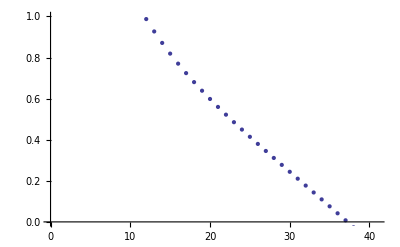

```mathematica
ListPlot[out,PlotRange->{0,1}]
```

## Iterations in C

Iterations using C
We export the above expressions for the patch frequencies, reproductive values and relatedness coefficients to as well as the selection gradients for p_1,p_2 and m to C, to allow computation on a computer cluster.
During each timestep, we iterate the values of p_1, p_2 and m. During each successive iteration, we solve for the novel values of the patch frequencies, reproductive values and relatedness coefficients. 
Iteration continues until the selection gradients vanish.
C Code can be requested from the authors: a.kuijper@ucl.ac.uk

### Export to C: functions

```mathematica
exportDiffRecur[file_,sys_,lhs1_,lhs2_,step_,Tend_,delta_,boundfunc_]:=Module[{mainstr,iter},
mainstr="";
(* initialize the xtplus1 lhs *)
For[iter=1,iter<=Length[sys],iter++,
mainstr=mainstr<>"double "<>ToString[CForm[lhs1[[iter]]]]<>" = 0;\n";
];
(* now print the for loop to iterate the system *)
mainstr=mainstr<>"\n\n for (int rtime = 0; rtime < "<>ToString[Tend]<>"; ++rtime)\n{\n";
For[iter=1,iter<=Length[sys],iter++,
mainstr=mainstr<>ToString[CForm[lhs1[[iter]]]]<>" = "<>ToString[CForm[lhs2[[iter]]]]<>"+"<>ToString[CForm[step]]<>"*("<>ToString[CForm[sys[[iter]]]]<>");\n\n";
];
(* now print the delta checking *)
mainstr=mainstr<>"\nif(\n";
For[iter=1,iter≤Length[sys],iter++,
mainstr=mainstr<>"fabs("<>ToString[CForm[lhs1[[iter]]]]<>"-"<>ToString[CForm[lhs2[[iter]]]]<>")<"<>ToString[CForm[delta]]<>"\n\t\t&& ";
];
(* erase last && and close if parentheses *)
mainstr=StringTake[mainstr,StringLength[mainstr]-3]<>")\n{\n";
(* put values from tplus1 to t *)
For[iter=1,iter≤Length[sys],iter++,
mainstr=mainstr<>ToString[CForm[lhs2[[iter]]]]<>"="<>ToString[boundfunc]<>"("<>ToString[CForm[lhs1[[iter]]]]<>");\n";
];
(* end if statement *)
mainstr=mainstr<>"\n\t break;\n}\n";
(* put values from tplus1 to t *)
For[iter=1,iter≤Length[sys],iter++,
mainstr=mainstr<>ToString[CForm[lhs2[[iter]]]]<>"="<>ToString[boundfunc]<>"("<>ToString[CForm[lhs1[[iter]]]]<>");\n";
];
(* end for loop *)
mainstr=mainstr<>"\n}\n\n";

For[iter=1,iter≤Length[sys],iter++,
mainstr=mainstr<>"gsl_vector_set(f,"<>ToString[iter-1]<>","<>ToString[CForm[lhs2[[iter]]]]<>");\n";
];
Export[file,mainstr];
]
```

```mathematica
(* export all the variables used *)
exportvarStruct[file_,vars_]:=Module[{str,iter},
str="";
For[iter=1,iter≤Length[vars],iter++,
str=str<>"double "<>ToString[CForm[vars[[iter]]]]<>";\n";
];
Export[file,str<>"\n\n"];
]
(* export those variables that are also parameters *)
exportParamStruct[file_,vars_]:=Module[{str,iter},
str="";
For[iter=1,iter≤Length[vars],iter++,
str=str<>"double "<>ToString[CForm[vars[[iter]]]]<>";\n";
];
Export[file,str<>"\n\n"];
]
```

### Export patch frequency recursions

```mathematica
lhs1patch=Table[ftplus1[es,nfa,nma],{es,1,2},{nfa,0,nf},{nma,0,nm}]//Flatten
lhs2patch=Table[f[es,nfa,nma],{es,1,2},{nfa,0,nf},{nma,0,nm}]//Flatten
```

{ftplus1[1,0,0],ftplus1[1,0,1],ftplus1[1,1,0],ftplus1[1,1,1],ftplus1[2,0,0],ftplus1[2,0,1],ftplus1[2,1,0],ftplus1[2,1,1]}

{fx[1,0,0],fx[1,0,1],fx[1,1,0],fx[1,1,1],fx[2,0,0],fx[2,0,1],fx[2,1,0],fx[2,1,1]}

```mathematica
exportDiffRecur[$HomeDirectory<>"/Projects/Transgeneration/msparentaleffects1/src/patchrecurs.txt",feqtabPlain,lhs1patch,lhs2patch,0.01,1000000,10^(-7),bound01]
```

### Export reproductive value recursions

```mathematica
vvecFlhs1=Flatten[Table[vtplus1[F,es,state,af,am],{es,1,2},{state,0,1},{af,0,nf-1},{am,0,nm}]];
vvecMlhs1=Flatten[Table[vtplus1[M,es,state,af,am],{es,1,2},{state,0,1},{af,0,nf},{am,0,nm-1}]];
vveclhs1=Join[vvecFlhs1,vvecMlhs1]
```

{vtplus1[F,1,0,0,0],vtplus1[F,1,0,0,1],vtplus1[F,1,1,0,0],vtplus1[F,1,1,0,1],vtplus1[F,2,0,0,0],vtplus1[F,2,0,0,1],vtplus1[F,2,1,0,0],vtplus1[F,2,1,0,1],vtplus1[M,1,0,0,0],vtplus1[M,1,0,1,0],vtplus1[M,1,1,0,0],vtplus1[M,1,1,1,0],vtplus1[M,2,0,0,0],vtplus1[M,2,0,1,0],vtplus1[M,2,1,0,0],vtplus1[M,2,1,1,0]}

```mathematica
exportDiffRecur[$HomeDirectory<>"/Projects/Transgeneration/msparentaleffects1/src/repvals.txt",Flatten[veqtabPlain],vveclhs1,vvec,0.01,1000000,10^(-7),bound0]
```

### Export relatedness recursions

```mathematica
lhs2relatedness=Table[x[[1]],{x,reltab}]
```

{r[aF,aM,1,1,1],r[aF,aM,2,1,1],r[aF,mM,1,1,0],r[aF,mM,2,1,0],r[mF,aM,1,0,1],r[mF,aM,2,0,1],r[mF,mM,1,0,0],r[mF,mM,2,0,0],F[aM,1,0,1],F[aM,1,1,1],F[aM,2,0,1],F[aM,2,1,1],F[mM,1,0,0],F[mM,1,1,0],F[mM,2,0,0],F[mM,2,1,0],F[aF,1,1,0],F[aF,1,1,1],F[aF,2,1,0],F[aF,2,1,1],F[mF,1,0,0],F[mF,1,0,1],F[mF,2,0,0],F[mF,2,0,1]}

```mathematica
lhs1relatedness=lhs2relatedness/.{r->rtplus1,F->Ftplus1}
```

{rtplus1[aF,aM,1,1,1],rtplus1[aF,aM,2,1,1],rtplus1[aF,mM,1,1,0],rtplus1[aF,mM,2,1,0],rtplus1[mF,aM,1,0,1],rtplus1[mF,aM,2,0,1],rtplus1[mF,mM,1,0,0],rtplus1[mF,mM,2,0,0],Ftplus1[aM,1,0,1],Ftplus1[aM,1,1,1],Ftplus1[aM,2,0,1],Ftplus1[aM,2,1,1],Ftplus1[mM,1,0,0],Ftplus1[mM,1,1,0],Ftplus1[mM,2,0,0],Ftplus1[mM,2,1,0],Ftplus1[aF,1,1,0],Ftplus1[aF,1,1,1],Ftplus1[aF,2,1,0],Ftplus1[aF,2,1,1],Ftplus1[mF,1,0,0],Ftplus1[mF,1,0,1],Ftplus1[mF,2,0,0],Ftplus1[mF,2,0,1]}

```mathematica
exportDiffRecur[$HomeDirectory<>"/Projects/Transgeneration/msparentaleffects1/src/relatedness.txt",Table[x[[2]]-x[[1]],{x,reltab}]/.replacerel,lhs1relatedness,lhs2relatedness,0.01,1000000,10^(-7),bound01]
```

```mathematica
mainrecursion[file_,lhs1_,lhs2_,sys_,step_,boundfunc_]:=Module[{mainstr,iter},
mainstr="";
For[iter=1,iter≤Length[sys],iter++,
mainstr=mainstr<>"double "<>ToString[CForm[lhs1[[iter]]]]<>";\n";
];
For[iter=1,iter<=Length[sys],iter++,
mainstr=mainstr<>ToString[CForm[lhs1[[iter]]]]<>" = "<>ToString[CForm[boundfunc]]<>"("<>ToString[CForm[lhs2[[iter]]]]<>"+"<>ToString[CForm[step]]<>"*("<>ToString[CForm[sys[[iter]]]]<>"));\n\n";
];
For[iter=1,iter≤Length[sys],iter++,
mainstr=mainstr<>"gsl_vector_set(f,"<>ToString[iter-1]<>","<>ToString[CForm[lhs1[[iter]]]]<>");\n";
];
Export[file,mainstr];
]
```

```mathematica
mainrecursion[$HomeDirectory<>"/Projects/Transgeneration/msparentaleffects1/src2/selgrad.txt",{p1tplus1,p2tplus1,mtplus1},{p1,p2,mt},{dveqdp[dp1],dveqdp[dp2],dveqdm[dmt]},eul,bound01]
```

```mathematica
(* export all the variables including the parameters *)
```

```mathematica
exportvarStruct[$HomeDirectory<>"/Projects/Transgeneration/msparentaleffects1/src2/variables.txt",Join[{c1,c2,q1,q2,k,mt,p1,p2,s1,s2,i,t,Q,eul},vvec,lhs2patch,lhs2relatedness]]
```

```mathematica
exportParamStruct[$HomeDirectory<>"/Projects/Transgeneration/msparentaleffects1/src2/params.txt",{c1,c2,q1,q2,k,s1,s2,i,t,Q,eul}]
```